```mathematica
(*IMPORT VALUES*)
rfile = Import["/Users/cadedulaney/Downloads/TAMUResearch/copperSystem/constantsall.csv", "Data"];
rfile[[1;;24, 1;;241]]// TableForm

AMAC = rfile[[1, 1;;241]];
AACE=rfile[[2, 1;;241]];
ACUP= rfile[[3, 1;;241]];
CTR = rfile[[4, 1;;241]];
CU= rfile[[5, 1;;241]];
MAC= rfile[[6, 1;;241]];
ACE = rfile[[7, 1;;241]];
CUP= rfile[[8, 1;;241]];
ACOX = rfile[[9, 1;;241]];
COX= rfile[[10, 1;;241]];

Dimensions[COX]

kINL = rfile[[11, 1;;241]];
kAMACL= rfile[[12, 1;;241]];
kAACEL = rfile[[13, 1;;241]];
kACOXL= rfile[[14, 1;;241]];
kACUPL = rfile[[15, 1;;241]];
kCTRL= rfile[[16, 1;;241]];
kMACFL = rfile[[17, 1;;241]];
kMACRL= rfile[[18, 1;;241]];
kACEFL = rfile[[19, 1;;241]];
kACERL= rfile[[20, 1;;241]];
kCUPFL = rfile[[21, 1;;241]];
kCUPRL= rfile[[22, 1;;241]];
kCOXFL = rfile[[23, 1;;241]];
kCOXRL= rfile[[24, 1;;241]];

(*SET GLOBAL VARIABLES*)
MCOXR = 0.1;
MCUPR = 0.1;
MACER = 0.1;
MMACR = 0.1;

ALPHA = 0.003333;
(*COPPERC = 14;*)
COPPER = 14;
SYSTEM = COPPER - 13;
KMIN = 10;
(*KNEW = 0.0004;*)
(*KNEW = 0.000656;*)
KNEW = 0.013;

(*38*)
While[SYSTEM < 241,
	(* SOLVING FOR K*)
	(*COPPER = COPPERC - CTR[[SYSTEM]] - CU[[SYSTEM]] - 4*MAC[[SYSTEM]]-4*ACE[[SYSTEM]]-8*CUP[[SYSTEM]] - COX[[SYSTEM]];*)
	(*COPPER = COPPERC;*)
	(*SOLVING NULL SPACE*)
	Print[SYSTEM];

	DAACE = ALPHA * AACE[[SYSTEM]];
	DACE = ALPHA * ACE[[SYSTEM]];
	DACOX = ALPHA * ACOX[[SYSTEM]];
	DCOX = ALPHA * COX[[SYSTEM]];
	DCTR = ALPHA * CTR[[SYSTEM]];
	DACUP = ALPHA * ACUP[[SYSTEM]];
	DCUP = ALPHA * CUP[[SYSTEM]];
	DAMAC = ALPHA * AMAC[[SYSTEM]];
	DMAC = ALPHA * MAC[[SYSTEM]];
	DCU = ALPHA * CU[[SYSTEM]];
	
	MMACF = MMACR + DMAC;
	MACEF = MACER + DACE;
	MCUPF = MCUPR + DCUP;
	MCOXF = MCOXR + DCOX;
	BCTR = DCTR;
	BMAC = MMACF - MMACR + DAMAC;
	BACE = MACEF - MACER + DAACE;
	BCOX = MCOXF - MCOXR + DACOX;
	BCUP = MCUPF - MCUPR + DACUP;
	CUIN = 4*MMACF + 4*MACEF + 8*MCUPF + MCOXF - 4*MMACR - 4*MACER - 8*MCUPR - MCOXR + DCU;
	
	(*GETTING K values*)
	(*eq1 = CUIN == (kIN * CTR[[SYSTEM]] * COPPER / (KMIN +COPPER)) + KNEW*COPPER;*)
	(*eq1 = CUIN == (kIN * CTR[[SYSTEM]] * COPPER / (KMIN +COPPER));*)
	eq1 = CUIN == (kIN * CTR[[SYSTEM]] * COPPER / (KMIN +COPPER)) + KNEW*CTR[[SYSTEM]]*COPPER;
	eq2 =BMAC == kAMAC;
	eq3 = BACE == kAACE;
	eq4 = BCOX == kACOX;
	eq5 = BCUP == kACUP * ACE[[SYSTEM]]^2;
	eq6 = BCTR == kCTR * AMAC[[SYSTEM]];
	eq7 = MMACF == kMACF * AMAC[[SYSTEM]] * CU[[SYSTEM]]^4;
	eq8 = MMACR == kMACR * MAC[[SYSTEM]];
	eq9 = MACEF == kACEF * AACE[[SYSTEM]] * CU[[SYSTEM]]^4;
	eq10 = MACER == kACER * ACE[[SYSTEM]];
	eq11 = MCUPF == kCUPF * ACUP[[SYSTEM]] * CU[[SYSTEM]]^8;
	eq12 = MCUPR == kCUPR * CUP[[SYSTEM]];
	eq13 = MCOXF == kCOXF * ACOX[[SYSTEM]] * CU[[SYSTEM]];
	eq14 = MCOXR == kCOXR * COX[[SYSTEM]];
	
	vars = {kIN, kAMAC, kAACE, kACOX, kACUP, kCTR, kMACF, kMACR, kACEF, kACER, kCUPF, kCUPR, kCOXF, kCOXR};
	solutions = NSolve[{eq1, eq2, eq3, eq4, eq5, eq6, eq7, eq8, eq9, eq10, eq11, eq12, eq13, eq14}, vars][[1]];
	MapThread[Set,{vars,vars/. solutions}];
	
	(*MAY NOT BE NECESSARY*)
	kINs  = kIN;
	kAMACs = kAMAC;
	kAACEs = kAACE;
	kACOXs = kACOX;
	kACUPs = kACUP;
	kCTRs = kCTR;
	kMACFs = kMACF;
	kMACRs = kMACR;
	kACEFs = kACEF;
	kACERs = kACER;
	kCUPFs = kCUPF;
	kCUPRs = kCUPR;
	kCOXFs = kCOXF;
	kCOXRs = kCOXR;

	Clear[kIN, kAMAC, kAACE, kACOX, kACUP, kCTR, kMACF, kMACR, kACEF, kACER, kCUPF, kCUPR, kCOXF, kCOXR];

	kINL[[SYSTEM]] = kINs;
	kAMACL[[SYSTEM]] = kAMACs;
	kAACEL[[SYSTEM]] = kAACEs;
	kACOXL[[SYSTEM]]= kACOXs;
	kACUPL[[SYSTEM]] = kACUPs;
	kCTRL[[SYSTEM]] = kCTRs;
	kMACFL[[SYSTEM]] = kMACFs;
	kMACRL[[SYSTEM]] = kMACRs;
	kACEFL[[SYSTEM]] = kACEFs;
	kACERL[[SYSTEM]] = kACERs;
	kCUPFL[[SYSTEM]] = kCUPFs;
	kCUPRL[[SYSTEM]] = kCUPRs;
	kCOXFL[[SYSTEM]] = kCOXFs;
	kCOXRL[[SYSTEM]] = kCOXRs;
	
	(*SET NEW COPPER VALUE*)
	(*COPPERC = COPPERC + 1;*)
	COPPER = COPPER +1;

	(*OBTAIN NEW CONC*)
	(*CUINC = (kINL [[SYSTEM]]* dCTR[t] * COPPER / (KMIN +COPPER)) + KNEW*COPPER;*)
	CUINC = (kINL [[SYSTEM]]* dCTR[t] * COPPER / (KMIN +COPPER)) + KNEW *CTR[[SYSTEM]]* COPPER;
	BMACC = kAMACL[[SYSTEM]];
	BACEC = kAACEL[[SYSTEM]];
	BCOXC = kACOXL[[SYSTEM]];
	BCUPC = kACUPL[[SYSTEM]] * dACE[t]^2;
	BCTRC = kCTRL[[SYSTEM]] * daMAC[t];
	MMACFC = kMACFL[[SYSTEM]] * daMAC[t] * dCU[t]^4;
	MMACRC = kMACRL[[SYSTEM]] * dMAC[t];
	MACEFC = kACEFL[[SYSTEM]] * daACE[t] * dCU[t]^4;
	MACERC = kACERL[[SYSTEM]] * dACE[t];
	MCUPFC = kCUPFL[[SYSTEM]] * daCUP[t] * dCU[t]^8;
	MCUPRC = kCUPRL[[SYSTEM]] * dCUP[t];
	MCOXFC = kCOXFL[[SYSTEM]] * daCOX[t] * dCU[t];
	MCOXRC = kCOXRL[[SYSTEM]] * dCOX[t];

	DAACEC = ALPHA * daACE[t];
	DACEC = ALPHA * dACE[t];
	DACOXC = ALPHA * daCOX[t];
	DCOXC = ALPHA * dCOX[t];
	DCTRC = ALPHA * dCTR[t];
	DACUPC = ALPHA * daCUP[t];
	DCUPC = ALPHA * dCUP[t];
	DAMACC = ALPHA * daMAC[t];
	DMACC = ALPHA * dMAC[t];
	DCUC = ALPHA * dCU[t];

	(*aMAC'*) diffeq1 = daMAC'[t] == BMACC - MMACFC + MMACRC - DAMACC;
	(*aACE'*)diffeq2 = daACE'[t] == BACEC - MACEFC + MACERC - DAACEC;
	(*aCUP'*)diffeq3 = daCUP'[t] ==BCUPC - MCUPFC + MCUPRC - DACUPC;
	(*CTR'*)diffeq4 = dCTR'[t] == BCTRC - DCTRC;
	(*CU'*)diffeq5 = dCU'[t] == CUINC - 4*MMACFC + 4*MMACRC - 4*MACEFC + 4*MACERC - 8*MCUPFC + 8*MCUPRC - MCOXFC + MCOXRC - DCUC;
	(*MAC'*)diffeq6 = dMAC'[t] == MMACFC - MMACRC - DMACC;
	(*ACE'*)diffeq7 = dACE'[t] == MACEFC - MACERC - DACEC;
	(*CUP'*)diffeq8 = dCUP'[t] == MCUPFC - MCUPRC - DCUPC;
	(*aCOX'*)diffeq9 = daCOX'[t] == BCOXC - MCOXFC + MCOXRC - DACOXC;
	(*COX'*)diffeq10 = dCOX'[t] == MCOXFC - MCOXRC - DCOXC;

	eqns={diffeq1,diffeq2,diffeq3,diffeq4,diffeq5,diffeq6,diffeq7,diffeq8, diffeq9, diffeq10, daMAC[0] == AMAC[[SYSTEM]], daACE[0] == ACE[[SYSTEM]], daCUP[0] == ACUP[[SYSTEM]], dCTR[0] == CTR[[SYSTEM]], dCU[0] == CU[[SYSTEM]], dMAC[0] == MAC[[SYSTEM]], dACE[0] == ACE[[SYSTEM]], dCUP[0] == CUP[[SYSTEM]], daCOX[0] == ACOX[[SYSTEM]], dCOX[0] == COX[[SYSTEM]]};
	s=NDSolve[eqns,{daMAC, daACE, daCUP, dCTR, dCU, dMAC, dACE, dCUP, daCOX, dCOX},{t,0,5000000}];
	<<NumericalCalculus`;
	
	daMACs = daMAC[5000000] /. s;
	daACEs = daACE[5000000] /. s;
	daCUPs = daCUP[5000000] /. s;
	daCTRs = dCTR[5000000] /. s;
	daCUs = dCU[5000000] /. s;
	dMACs = dMAC[5000000] /. s;
	dACEs = dACE[5000000] /. s;
	dCUPs = dCUP[5000000] /. s;
	daCOXs = daCOX[5000000] /. s;
	dCOXs = dCOX[5000000] /. s;

	SYSTEM = SYSTEM + 1;

	AMAC[[SYSTEM]]=daMACs[[1]];
	AACE[[SYSTEM]]=daACEs[[1]];
	ACUP[[SYSTEM]]=daCUPs[[1]];
	CTR[[SYSTEM]]=daCTRs[[1]];
	CU[[SYSTEM]]=daCUs[[1]];
	MAC[[SYSTEM]]=dMACs[[1]];
	ACE[[SYSTEM]]=dACEs[[1]];
	CUP[[SYSTEM]]=dCUPs[[1]];
	ACOX[[SYSTEM]]=daCOXs[[1]];
	COX[[SYSTEM]]=dCOXs[[1]];
]

Print["Done"]
Export["/Users/cadedulaney/Downloads/TAMUResearch/copperSystem/constantsall.csv",{AMAC, AACE, ACUP, CTR, CU, MAC, ACE, CUP, ACOX, COX, kINL, kAMACL, kAACEL, kACOXL, kACUPL, kCTRL, kMACFL, kMACRL, kACEFL, kACERL, kCUPFL, kCUPRL, kCOXFL, kCOXRL}];
```

0.1914 | 0.0834655 | 0.0788872 | 0.0747693 | 0.0710514 | 0.0676818 | 0.0646165 | 0.0618182 | 0.0592548 | 0.0568989 | 0.054727 | 0.0527189 | 0.0508571 | 0.0491263 | 0.0475134 | 0.0460067 | 0.0445963 | 0.0432731 | 0.0420294 | 0.0408581 | 0.0397532 | 0.038709 | 0.0377207 | 0.0367838 | 0.0358945 | 0.0350491 | 0.0342445 | 0.0334776 | 0.032746 | 0.0320471 | 0.0313788 | 0.0307391 | 0.0301262 | 0.0295384 | 0.0289741 | 0.028432 | 0.0279107 | 0.027409 | 0.0269259 | 0.0264603 | 0.0260112 | 0.0255779 | 0.0251593 | 0.0247548 | 0.0243637 | 0.0239853 | 0.023619 | 0.0232642 | 0.0229203 | 0.0225869 | 0.0222634 | 0.0219495 | 0.0216446 | 0.0213485 | 0.0210606 | 0.0207808 | 0.0205086 | 0.0202437 | 0.0199858 | 0.0197346 | 0.01949 | 0.0192515 | 0.0190191 | 0.0187924 | 0.0185713 | 0.0183554 | 0.0181448 | 0.0179391 | 0.0177381 | 0.0175418 | 0.0173499 | 0.0171624 | 0.0169789 | 0.0167996 | 0.016624 | 0.0164523 | 0.0162841 | 0.0161195 | 0.0159583 | 0.0158004 | 0.0156457 | 0.0154941 | 0.0153455 | 0.0151998 | 0.015057 | 0.0149168 | 0.0147794 | 0.0146445 | 0.0145122 | 0.0143823 | 0.0142548 | 0.0141296 | 0.0140066 | 0.0138858 | 0.0137672 | 0.0136506 | 0.013536 | 0.0134234 | 0.0133127 | 0.0132039 | 0.0130969 | 0.0129917 | 0.0128882 | 0.0127863 | 0.0126861 | 0.0125876 | 0.0124905 | 0.012395 | 0.012301 | 0.0122085 | 0.0121173 | 0.0120276 | 0.0119392 | 0.0118521 | 0.0117664 | 0.0116819 | 0.0115986 | 0.0115165 | 0.0114357 | 0.011356 | 0.0112774 | 0.0111999 | 0.0111235 | 0.0110482 | 0.0109739 | 0.0109006 | 0.0108283 | 0.010757 | 0.0106867 | 0.0106173 | 0.0105488 | 0.0104812 | 0.0104145 | 0.0103486 | 0.0102836 | 0.0102195 | 0.0101561 | 0.0100936 | 0.0100318 | 0.00997081 | 0.00991057 | 0.00985107 | 0.00979229 | 0.00973423 | 0.00967687 | 0.0096202 | 0.0095642 | 0.00950886 | 0.00945418 | 0.00940014 | 0.00934672 | 0.00929393 | 0.00924174 | 0.00919014 | 0.00913913 | 0.0090887 | 0.00903883 | 0.00898952 | 0.00894076 | 0.00889254 | 0.00884484 | 0.00879766 | 0.008751 | 0.00870484 | 0.00865917 | 0.00861399 | 0.00856929 | 0.00852506 | 0.0084813 | 0.00843799 | 0.00839514 | 0.00835272 | 0.00831074 | 0.00826919 | 0.00822806 | 0.00818735 | 0.00814704 | 0.00810714 | 0.00806764 | 0.00802853 | 0.0079898 | 0.00795146 | 0.00791348 | 0.00787588 | 0.00783864 | 0.00780175 | 0.00776522 | 0.00772904 | 0.0076932 | 0.0076577 | 0.00762253 | 0.00758768 | 0.00755317 | 0.00751897 | 0.00748508 | 0.00745151 | 0.00741824 | 0.00738527 | 0.0073526 | 0.00732023 | 0.00728814 | 0.00725634 | 0.00722482 | 0.00719358 | 0.00716262 | 0.00713192 | 0.00710149 | 0.00707133 | 0.00704142 | 0.00701178 | 0.00698238 | 0.00695324 | 0.00692434 | 0.00689569 | 0.00686728 | 0.0068391 | 0.00681116 | 0.00678346 | 0.00675598 | 0.00672873 | 0.0067017 | 0.00667489 | 0.0066483 | 0.00662192 | 0.00659576 | 0.0065698 | 0.00654406 | 0.00651852 | 0.00649318 | 0.00646804 | 0.0064431 | 0.00641835 | 0.0063938 | 0.00636944 | 0.00634526 | 0.00632127 | 0.00629747 | 0.00627385 | 0.00625041 | 0.00622715 | 0.00620406
0.2325 | 0.101388 | 0.0958269 | 0.0908248 | 0.0863085 | 0.0822153 | 0.0784919 | 0.0750926 | 0.0719788 | 0.069117 | 0.0664788 | 0.0640394 | 0.0617778 | 0.0596753 | 0.0577161 | 0.0558859 | 0.0541726 | 0.0525653 | 0.0510545 | 0.0496318 | 0.0482895 | 0.0470211 | 0.0458206 | 0.0446826 | 0.0436023 | 0.0425754 | 0.0415979 | 0.0406664 | 0.0397777 | 0.0389287 | 0.0381169 | 0.0373399 | 0.0365953 | 0.0358813 | 0.0351958 | 0.0345373 | 0.0339041 | 0.0332947 | 0.0327078 | 0.0321422 | 0.0315967 | 0.0310703 | 0.0305618 | 0.0300705 | 0.0295954 | 0.0291358 | 0.0286908 | 0.0282598 | 0.027842 | 0.027437 | 0.0270441 | 0.0266627 | 0.0262924 | 0.0259327 | 0.0255831 | 0.0252431 | 0.0249124 | 0.0245906 | 0.0242774 | 0.0239723 | 0.0236751 | 0.0233855 | 0.0231031 | 0.0228278 | 0.0225591 | 0.022297 | 0.0220411 | 0.0217912 | 0.0215471 | 0.0213086 | 0.0210755 | 0.0208477 | 0.0206249 | 0.020407 | 0.0201938 | 0.0199851 | 0.0197809 | 0.0195809 | 0.0193851 | 0.0191933 | 0.0190054 | 0.0188212 | 0.0186407 | 0.0184637 | 0.0182902 | 0.01812 | 0.017953 | 0.0177892 | 0.0176284 | 0.0174707 | 0.0173158 | 0.0171637 | 0.0170143 | 0.0168676 | 0.0167234 | 0.0165818 | 0.0164427 | 0.0163059 | 0.0161714 | 0.0160392 | 0.0159093 | 0.0157814 | 0.0156557 | 0.015532 | 0.0154103 | 0.0152905 | 0.0151727 | 0.0150567 | 0.0149425 | 0.01483 | 0.0147193 | 0.0146103 | 0.014503 | 0.0143972 | 0.014293 | 0.0141904 | 0.0140892 | 0.0139895 | 0.0138913 | 0.0137945 | 0.013699 | 0.0136049 | 0.0135121 | 0.0134206 | 0.0133303 | 0.0132413 | 0.0131535 | 0.0130669 | 0.0129815 | 0.0128972 | 0.012814 | 0.0127319 | 0.0126508 | 0.0125708 | 0.0124919 | 0.0124139 | 0.012337 | 0.012261 | 0.012186 | 0.0121119 | 0.0120387 | 0.0119664 | 0.011895 | 0.0118245 | 0.0117548 | 0.011686 | 0.011618 | 0.0115507 | 0.0114843 | 0.0114187 | 0.0113538 | 0.0112896 | 0.0112262 | 0.0111636 | 0.0111016 | 0.0110403 | 0.0109798 | 0.0109199 | 0.0108606 | 0.0108021 | 0.0107441 | 0.0106868 | 0.0106301 | 0.0105741 | 0.0105186 | 0.0104637 | 0.0104094 | 0.0103557 | 0.0103025 | 0.0102499 | 0.0101979 | 0.0101463 | 0.0100953 | 0.0100449 | 0.0099949 | 0.00994545 | 0.00989649 | 0.00984802 | 0.00980003 | 0.00975252 | 0.00970548 | 0.0096589 | 0.00961277 | 0.00956709 | 0.00952186 | 0.00947705 | 0.00943268 | 0.00938872 | 0.00934519 | 0.00930206 | 0.00925934 | 0.00921701 | 0.00917508 | 0.00913354 | 0.00909238 | 0.0090516 | 0.00901118 | 0.00897114 | 0.00893145 | 0.00889212 | 0.00885315 | 0.00881452 | 0.00877623 | 0.00873828 | 0.00870067 | 0.00866338 | 0.00862642 | 0.00858978 | 0.00855345 | 0.00851744 | 0.00848173 | 0.00844633 | 0.00841123 | 0.00837643 | 0.00834191 | 0.00830769 | 0.00827375 | 0.00824009 | 0.00820671 | 0.00817361 | 0.00814078 | 0.00810821 | 0.00807591 | 0.00804387 | 0.00801209 | 0.00798056 | 0.00794929 | 0.00791826 | 0.00788748 | 0.00785694 | 0.00782665 | 0.00779659 | 0.00776676 | 0.00773717 | 0.0077078 | 0.00767866 | 0.00764975 | 0.00762106 | 0.00759258 | 0.00756432 | 0.00753628
0.2198 | 0.0388105 | 0.0336294 | 0.0293375 | 0.0257578 | 0.0227517 | 0.0202101 | 0.018047 | 0.0161946 | 0.0145987 | 0.013216 | 0.0120115 | 0.010957 | 0.0100294 | 0.00920982 | 0.00848254 | 0.00783461 | 0.00725522 | 0.00673527 | 0.00626711 | 0.00584424 | 0.00546115 | 0.0051131 | 0.00479605 | 0.0045065 | 0.00424142 | 0.00399819 | 0.00377452 | 0.0035684 | 0.0033781 | 0.00320205 | 0.0030389 | 0.00288745 | 0.00274661 | 0.00261544 | 0.0024931 | 0.00237881 | 0.00227191 | 0.00217178 | 0.00207787 | 0.00198968 | 0.00190678 | 0.00182874 | 0.00175521 | 0.00168586 | 0.00162037 | 0.00155847 | 0.00149991 | 0.00144445 | 0.00139189 | 0.00134203 | 0.0012947 | 0.00124971 | 0.00120694 | 0.00116623 | 0.00112747 | 0.00109052 | 0.00105528 | 0.00102165 | 0.000989536 | 0.000958846 | 0.0009295 | 0.000901422 | 0.000874543 | 0.000848795 | 0.000824118 | 0.000800455 | 0.000777751 | 0.000755956 | 0.000735024 | 0.00071491 | 0.000695574 | 0.000676976 | 0.000659081 | 0.000641853 | 0.000625261 | 0.000609275 | 0.000593866 | 0.000579008 | 0.000564674 | 0.000550841 | 0.000537487 | 0.00052459 | 0.000512129 | 0.000500087 | 0.000488444 | 0.000477184 | 0.000466291 | 0.000455748 | 0.000445542 | 0.000435659 | 0.000426085 | 0.000416808 | 0.000407816 | 0.000399098 | 0.000390642 | 0.00038244 | 0.000374481 | 0.000366756 | 0.000359255 | 0.000351971 | 0.000344895 | 0.00033802 | 0.000331339 | 0.000324844 | 0.000318528 | 0.000312386 | 0.000306411 | 0.000300597 | 0.000294939 | 0.000289431 | 0.000284068 | 0.000278845 | 0.000273758 | 0.000268802 | 0.000263972 | 0.000259265 | 0.000254676 | 0.000250202 | 0.000245838 | 0.000241582 | 0.00023743 | 0.000233379 | 0.000229425 | 0.000225565 | 0.000221797 | 0.000218118 | 0.000214525 | 0.000211016 | 0.000207587 | 0.000204237 | 0.000200963 | 0.000197764 | 0.000194636 | 0.000191578 | 0.000188587 | 0.000185663 | 0.000182802 | 0.000180004 | 0.000177266 | 0.000174587 | 0.000171964 | 0.000169398 | 0.000166885 | 0.000164425 | 0.000162016 | 0.000159657 | 0.000157346 | 0.000155083 | 0.000152865 | 0.000150692 | 0.000148563 | 0.000146476 | 0.00014443 | 0.000142425 | 0.000140459 | 0.000138531 | 0.000136641 | 0.000134786 | 0.000132968 | 0.000131184 | 0.000129433 | 0.000127716 | 0.000126031 | 0.000124377 | 0.000122754 | 0.00012116 | 0.000119596 | 0.00011806 | 0.000116552 | 0.000115071 | 0.000113617 | 0.000112189 | 0.000110786 | 0.000109407 | 0.000108053 | 0.000106723 | 0.000105415 | 0.00010413 | 0.000102868 | 0.000101626 | 0.000100406 | 0.0000992068 | 0.0000980276 | 0.0000968682 | 0.000095728 | 0.0000946068 | 0.0000935041 | 0.0000924196 | 0.0000913527 | 0.0000903032 | 0.0000892708 | 0.0000882549 | 0.0000872554 | 0.0000862718 | 0.0000853038 | 0.0000843512 | 0.0000834135 | 0.0000824906 | 0.000081582 | 0.0000806876 | 0.000079807 | 0.0000789399 | 0.0000780861 | 0.0000772453 | 0.0000764173 | 0.0000756018 | 0.0000747986 | 0.0000740074 | 0.000073228 | 0.0000724601 | 0.0000717036 | 0.0000709583 | 0.0000702239 | 0.0000695002 | 0.000068787 | 0.0000680841 | 0.0000673913 | 0.0000667085 | 0.0000660354 | 0.000065372 | 0.0000647179 | 0.000064073 | 0.0000634372 | 0.0000628103 | 0.0000621921 | 0.0000615825 | 0.0000609813 | 0.0000603884 | 0.0000598036 | 0.0000592268 | 0.0000586579 | 0.0000580966 | 0.000057543 | 0.0000569967 | 0.0000564578 | 0.000055926 | 0.0000554014 | 0.0000548836 | 0.0000543727 | 0.0000538685
0.3889 | 0.169591 | 0.160289 | 0.151922 | 0.144367 | 0.137521 | 0.131292 | 0.125607 | 0.120398 | 0.115611 | 0.111198 | 0.107118 | 0.103335 | 0.0998182 | 0.096541 | 0.0934797 | 0.0906139 | 0.0879254 | 0.0853983 | 0.0830185 | 0.0807733 | 0.0786517 | 0.0766435 | 0.07474 | 0.072933 | 0.0712153 | 0.0695803 | 0.0680222 | 0.0665356 | 0.0651156 | 0.0637577 | 0.0624579 | 0.0612126 | 0.0600182 | 0.0588716 | 0.0577701 | 0.0567109 | 0.0556916 | 0.05471 | 0.0537639 | 0.0528515 | 0.0519709 | 0.0511204 | 0.0502986 | 0.0495039 | 0.048735 | 0.0479907 | 0.0472698 | 0.0465711 | 0.0458936 | 0.0452364 | 0.0445985 | 0.0439791 | 0.0433773 | 0.0427925 | 0.0422238 | 0.0416707 | 0.0411325 | 0.0406085 | 0.0400982 | 0.0396011 | 0.0391167 | 0.0386443 | 0.0381837 | 0.0377344 | 0.0372959 | 0.0368678 | 0.0364498 | 0.0360416 | 0.0356427 | 0.0352528 | 0.0348717 | 0.034499 | 0.0341345 | 0.0337779 | 0.0334289 | 0.0330873 | 0.0327528 | 0.0324253 | 0.0321044 | 0.0317901 | 0.031482 | 0.0311801 | 0.0308841 | 0.0305938 | 0.0303091 | 0.0300298 | 0.0297558 | 0.0294869 | 0.029223 | 0.0289639 | 0.0287094 | 0.0284596 | 0.0282142 | 0.0279731 | 0.0277362 | 0.0275035 | 0.0272747 | 0.0270498 | 0.0268286 | 0.0266112 | 0.0263974 | 0.0261871 | 0.0259802 | 0.0257766 | 0.0255763 | 0.0253791 | 0.0251851 | 0.0249941 | 0.024806 | 0.0246209 | 0.0244385 | 0.0242589 | 0.024082 | 0.0239077 | 0.023736 | 0.0235669 | 0.0234001 | 0.0232358 | 0.0230738 | 0.0229141 | 0.0227567 | 0.0226015 | 0.0224484 | 0.0222975 | 0.0221486 | 0.0220017 | 0.0218569 | 0.0217139 | 0.0215729 | 0.0214338 | 0.0212964 | 0.0211609 | 0.0210271 | 0.020895 | 0.0207646 | 0.0206359 | 0.0205088 | 0.0203833 | 0.0202594 | 0.020137 | 0.0200161 | 0.0198967 | 0.0197787 | 0.0196621 | 0.019547 | 0.0194332 | 0.0193208 | 0.0192097 | 0.0190999 | 0.0189913 | 0.0188841 | 0.018778 | 0.0186732 | 0.0185695 | 0.0184671 | 0.0183657 | 0.0182655 | 0.0181665 | 0.0180685 | 0.0179716 | 0.0178757 | 0.0177809 | 0.0176871 | 0.0175943 | 0.0175025 | 0.0174117 | 0.0173218 | 0.0172329 | 0.0171449 | 0.0170578 | 0.0169716 | 0.0168863 | 0.0168019 | 0.0167184 | 0.0166356 | 0.0165537 | 0.0164727 | 0.0163924 | 0.0163129 | 0.0162342 | 0.0161563 | 0.0160792 | 0.0160028 | 0.0159271 | 0.0158522 | 0.0157779 | 0.0157044 | 0.0156316 | 0.0155594 | 0.015488 | 0.0154172 | 0.0153471 | 0.0152776 | 0.0152087 | 0.0151405 | 0.0150729 | 0.0150059 | 0.0149395 | 0.0148738 | 0.0148086 | 0.0147439 | 0.0146799 | 0.0146164 | 0.0145535 | 0.0144911 | 0.0144293 | 0.014368 | 0.0143073 | 0.014247 | 0.0141873 | 0.0141281 | 0.0140694 | 0.0140111 | 0.0139534 | 0.0138962 | 0.0138394 | 0.0137831 | 0.0137273 | 0.0136719 | 0.013617 | 0.0135625 | 0.0135085 | 0.0134549 | 0.0134017 | 0.013349 | 0.0132967 | 0.0132448 | 0.0131933 | 0.0131422 | 0.0130915 | 0.0130413 | 0.0129914 | 0.0129419 | 0.0128928 | 0.012844 | 0.0127956 | 0.0127477 | 0.0127 | 0.0126528 | 0.0126058
0.5578 | 0.767611 | 0.781473 | 0.794687 | 0.807303 | 0.819368 | 0.830925 | 0.842014 | 0.852671 | 0.862927 | 0.872812 | 0.882352 | 0.891572 | 0.900493 | 0.909136 | 0.917517 | 0.925653 | 0.93356 | 0.941252 | 0.948739 | 0.956035 | 0.96315 | 0.970093 | 0.976874 | 0.9835 | 0.98998 | 0.99632 | 1.00253 | 1.00861 | 1.01457 | 1.02041 | 1.02615 | 1.03178 | 1.0373 | 1.04273 | 1.04807 | 1.05332 | 1.05848 | 1.06355 | 1.06855 | 1.07347 | 1.07832 | 1.08309 | 1.0878 | 1.09244 | 1.09701 | 1.10152 | 1.10597 | 1.11036 | 1.11469 | 1.11897 | 1.12319 | 1.12737 | 1.13149 | 1.13556 | 1.13958 | 1.14356 | 1.14749 | 1.15138 | 1.15523 | 1.15903 | 1.16279 | 1.16652 | 1.1702 | 1.17385 | 1.17746 | 1.18103 | 1.18457 | 1.18807 | 1.19154 | 1.19498 | 1.19839 | 1.20176 | 1.2051 | 1.20842 | 1.2117 | 1.21496 | 1.21818 | 1.22138 | 1.22455 | 1.2277 | 1.23082 | 1.23391 | 1.23698 | 1.24002 | 1.24304 | 1.24604 | 1.24901 | 1.25196 | 1.25489 | 1.2578 | 1.26068 | 1.26355 | 1.26639 | 1.26921 | 1.27201 | 1.27479 | 1.27756 | 1.2803 | 1.28302 | 1.28573 | 1.28842 | 1.29109 | 1.29374 | 1.29637 | 1.29899 | 1.30159 | 1.30417 | 1.30674 | 1.30929 | 1.31183 | 1.31435 | 1.31685 | 1.31934 | 1.32182 | 1.32428 | 1.32672 | 1.32915 | 1.33157 | 1.33397 | 1.33636 | 1.33873 | 1.34109 | 1.34344 | 1.34578 | 1.3481 | 1.35041 | 1.35271 | 1.35499 | 1.35726 | 1.35952 | 1.36177 | 1.36401 | 1.36623 | 1.36845 | 1.37065 | 1.37284 | 1.37502 | 1.37719 | 1.37935 | 1.38149 | 1.38363 | 1.38576 | 1.38787 | 1.38998 | 1.39207 | 1.39416 | 1.39623 | 1.3983 | 1.40036 | 1.4024 | 1.40444 | 1.40647 | 1.40849 | 1.4105 | 1.4125 | 1.41449 | 1.41647 | 1.41844 | 1.42041 | 1.42236 | 1.42431 | 1.42625 | 1.42818 | 1.43011 | 1.43202 | 1.43393 | 1.43583 | 1.43772 | 1.4396 | 1.44147 | 1.44334 | 1.4452 | 1.44705 | 1.4489 | 1.45074 | 1.45257 | 1.45439 | 1.4562 | 1.45801 | 1.45981 | 1.46161 | 1.46339 | 1.46518 | 1.46695 | 1.46872 | 1.47048 | 1.47223 | 1.47398 | 1.47572 | 1.47745 | 1.47918 | 1.4809 | 1.48261 | 1.48432 | 1.48603 | 1.48772 | 1.48941 | 1.4911 | 1.49277 | 1.49445 | 1.49611 | 1.49777 | 1.49943 | 1.50108 | 1.50272 | 1.50436 | 1.50599 | 1.50762 | 1.50924 | 1.51085 | 1.51246 | 1.51407 | 1.51567 | 1.51726 | 1.51885 | 1.52043 | 1.52201 | 1.52358 | 1.52515 | 1.52671 | 1.52827 | 1.52982 | 1.53137 | 1.53292 | 1.53445 | 1.53599 | 1.53752 | 1.53904 | 1.54056 | 1.54207 | 1.54358 | 1.54509 | 1.54659 | 1.54808 | 1.54957 | 1.55106 | 1.55254 | 1.55402 | 1.55549 | 1.55696
0.1914 | 0.299335 | 0.303913 | 0.308031 | 0.311749 | 0.315118 | 0.318183 | 0.320982 | 0.323545 | 0.325901 | 0.328073 | 0.330081 | 0.331943 | 0.333674 | 0.335287 | 0.336793 | 0.338204 | 0.339527 | 0.340771 | 0.341942 | 0.343047 | 0.344091 | 0.345079 | 0.346016 | 0.346905 | 0.347751 | 0.348556 | 0.349322 | 0.350054 | 0.350753 | 0.351421 | 0.352061 | 0.352674 | 0.353262 | 0.353826 | 0.354368 | 0.354889 | 0.355391 | 0.355874 | 0.35634 | 0.356789 | 0.357222 | 0.357641 | 0.358045 | 0.358436 | 0.358815 | 0.359181 | 0.359536 | 0.35988 | 0.360213 | 0.360537 | 0.360851 | 0.361155 | 0.361452 | 0.361739 | 0.362019 | 0.362291 | 0.362556 | 0.362814 | 0.363065 | 0.36331 | 0.363548 | 0.363781 | 0.364008 | 0.364229 | 0.364445 | 0.364655 | 0.364861 | 0.365062 | 0.365258 | 0.36545 | 0.365638 | 0.365821 | 0.366 | 0.366176 | 0.366348 | 0.366516 | 0.36668 | 0.366842 | 0.367 | 0.367154 | 0.367306 | 0.367454 | 0.3676 | 0.367743 | 0.367883 | 0.368021 | 0.368155 | 0.368288 | 0.368418 | 0.368545 | 0.36867 | 0.368793 | 0.368914 | 0.369033 | 0.369149 | 0.369264 | 0.369377 | 0.369487 | 0.369596 | 0.369703 | 0.369808 | 0.369912 | 0.370014 | 0.370114 | 0.370212 | 0.370309 | 0.370405 | 0.370499 | 0.370592 | 0.370683 | 0.370772 | 0.370861 | 0.370948 | 0.371034 | 0.371118 | 0.371201 | 0.371283 | 0.371364 | 0.371444 | 0.371523 | 0.3716 | 0.371677 | 0.371752 | 0.371826 | 0.371899 | 0.371972 | 0.372043 | 0.372113 | 0.372183 | 0.372251 | 0.372319 | 0.372386 | 0.372451 | 0.372516 | 0.372581 | 0.372644 | 0.372706 | 0.372768 | 0.372829 | 0.372889 | 0.372949 | 0.373008 | 0.373066 | 0.373123 | 0.37318 | 0.373236 | 0.373291 | 0.373346 | 0.3734 | 0.373453 | 0.373506 | 0.373558 | 0.37361 | 0.373661 | 0.373711 | 0.373761 | 0.37381 | 0.373859 | 0.373907 | 0.373955 | 0.374002 | 0.374049 | 0.374095 | 0.374141 | 0.374186 | 0.374231 | 0.374275 | 0.374319 | 0.374362 | 0.374405 | 0.374447 | 0.374489 | 0.374531 | 0.374572 | 0.374613 | 0.374653 | 0.374693 | 0.374732 | 0.374771 | 0.37481 | 0.374849 | 0.374887 | 0.374924 | 0.374961 | 0.374998 | 0.375035 | 0.375071 | 0.375107 | 0.375142 | 0.375177 | 0.375212 | 0.375247 | 0.375281 | 0.375315 | 0.375348 | 0.375382 | 0.375415 | 0.375447 | 0.37548 | 0.375512 | 0.375544 | 0.375575 | 0.375606 | 0.375637 | 0.375668 | 0.375699 | 0.375729 | 0.375759 | 0.375788 | 0.375818 | 0.375847 | 0.375876 | 0.375904 | 0.375933 | 0.375961 | 0.375989 | 0.376017 | 0.376044 | 0.376071 | 0.376098 | 0.376125 | 0.376152 | 0.376178 | 0.376204 | 0.37623 | 0.376256 | 0.376281 | 0.376307 | 0.376332 | 0.376357 | 0.376382 | 0.376406 | 0.376431 | 0.376455 | 0.376479 | 0.376503 | 0.376526 | 0.37655 | 0.376573 | 0.376596
0.2325 | 0.363612 | 0.369173 | 0.374175 | 0.378691 | 0.382785 | 0.386508 | 0.389907 | 0.393021 | 0.395883 | 0.398521 | 0.400961 | 0.403222 | 0.405325 | 0.407284 | 0.409114 | 0.410827 | 0.412435 | 0.413945 | 0.415368 | 0.41671 | 0.417979 | 0.419179 | 0.420317 | 0.421398 | 0.422425 | 0.423402 | 0.424334 | 0.425222 | 0.426071 | 0.426883 | 0.42766 | 0.428405 | 0.429119 | 0.429804 | 0.430463 | 0.431096 | 0.431705 | 0.432292 | 0.432858 | 0.433403 | 0.43393 | 0.434438 | 0.434929 | 0.435405 | 0.435864 | 0.436309 | 0.43674 | 0.437158 | 0.437563 | 0.437956 | 0.438337 | 0.438708 | 0.439067 | 0.439417 | 0.439757 | 0.440088 | 0.440409 | 0.440723 | 0.441028 | 0.441325 | 0.441614 | 0.441897 | 0.442172 | 0.442441 | 0.442703 | 0.442959 | 0.443209 | 0.443453 | 0.443691 | 0.443924 | 0.444152 | 0.444375 | 0.444593 | 0.444806 | 0.445015 | 0.445219 | 0.445419 | 0.445615 | 0.445807 | 0.445995 | 0.446179 | 0.446359 | 0.446536 | 0.44671 | 0.44688 | 0.447047 | 0.447211 | 0.447372 | 0.447529 | 0.447684 | 0.447836 | 0.447986 | 0.448132 | 0.448277 | 0.448418 | 0.448557 | 0.448694 | 0.448829 | 0.448961 | 0.449091 | 0.449219 | 0.449344 | 0.449468 | 0.44959 | 0.449709 | 0.449827 | 0.449943 | 0.450058 | 0.45017 | 0.450281 | 0.45039 | 0.450497 | 0.450603 | 0.450707 | 0.45081 | 0.450911 | 0.45101 | 0.451109 | 0.451206 | 0.451301 | 0.451395 | 0.451488 | 0.451579 | 0.45167 | 0.451759 | 0.451846 | 0.451933 | 0.452019 | 0.452103 | 0.452186 | 0.452268 | 0.452349 | 0.452429 | 0.452508 | 0.452586 | 0.452663 | 0.452739 | 0.452814 | 0.452888 | 0.452961 | 0.453034 | 0.453105 | 0.453176 | 0.453245 | 0.453314 | 0.453382 | 0.453449 | 0.453516 | 0.453581 | 0.453646 | 0.45371 | 0.453774 | 0.453836 | 0.453898 | 0.45396 | 0.45402 | 0.45408 | 0.454139 | 0.454198 | 0.454256 | 0.454313 | 0.45437 | 0.454426 | 0.454481 | 0.454536 | 0.454591 | 0.454644 | 0.454697 | 0.45475 | 0.454802 | 0.454854 | 0.454905 | 0.454955 | 0.455005 | 0.455055 | 0.455104 | 0.455152 | 0.4552 | 0.455247 | 0.455295 | 0.455341 | 0.455387 | 0.455433 | 0.455478 | 0.455523 | 0.455567 | 0.455611 | 0.455655 | 0.455698 | 0.455741 | 0.455783 | 0.455825 | 0.455866 | 0.455908 | 0.455948 | 0.455989 | 0.456029 | 0.456069 | 0.456108 | 0.456147 | 0.456185 | 0.456224 | 0.456262 | 0.456299 | 0.456337 | 0.456374 | 0.45641 | 0.456447 | 0.456483 | 0.456518 | 0.456554 | 0.456589 | 0.456624 | 0.456658 | 0.456692 | 0.456726 | 0.45676 | 0.456793 | 0.456826 | 0.456859 | 0.456892 | 0.456924 | 0.456956 | 0.456988 | 0.457019 | 0.457051 | 0.457082 | 0.457113 | 0.457143 | 0.457173 | 0.457203 | 0.457233 | 0.457263 | 0.457292 | 0.457321 | 0.45735 | 0.457379 | 0.457407 | 0.457436 | 0.457464
0.2689 | 1.15648 | 1.1985 | 1.23641 | 1.27073 | 1.30191 | 1.33035 | 1.35637 | 1.38027 | 1.40227 | 1.4226 | 1.44144 | 1.45893 | 1.47523 | 1.49044 | 1.50468 | 1.51803 | 1.53057 | 1.54238 | 1.55351 | 1.56403 | 1.57399 | 1.58342 | 1.59237 | 1.60088 | 1.60898 | 1.6167 | 1.62406 | 1.6311 | 1.63782 | 1.64426 | 1.65042 | 1.65634 | 1.66201 | 1.66747 | 1.67271 | 1.67776 | 1.68262 | 1.6873 | 1.69182 | 1.69618 | 1.70039 | 1.70446 | 1.70839 | 1.7122 | 1.71589 | 1.71946 | 1.72292 | 1.72627 | 1.72953 | 1.73269 | 1.73576 | 1.73874 | 1.74164 | 1.74445 | 1.7472 | 1.74986 | 1.75246 | 1.75499 | 1.75745 | 1.75985 | 1.7622 | 1.76448 | 1.76671 | 1.76888 | 1.771 | 1.77308 | 1.7751 | 1.77708 | 1.77901 | 1.7809 | 1.78275 | 1.78456 | 1.78633 | 1.78806 | 1.78976 | 1.79142 | 1.79304 | 1.79463 | 1.79619 | 1.79772 | 1.79922 | 1.80069 | 1.80213 | 1.80355 | 1.80493 | 1.80629 | 1.80763 | 1.80894 | 1.81023 | 1.81149 | 1.81273 | 1.81395 | 1.81515 | 1.81632 | 1.81748 | 1.81862 | 1.81973 | 1.82083 | 1.82191 | 1.82298 | 1.82402 | 1.82505 | 1.82606 | 1.82706 | 1.82804 | 1.829 | 1.82995 | 1.83089 | 1.83181 | 1.83271 | 1.83361 | 1.83449 | 1.83535 | 1.83621 | 1.83705 | 1.83788 | 1.83869 | 1.8395 | 1.84029 | 1.84108 | 1.84185 | 1.84261 | 1.84336 | 1.8441 | 1.84483 | 1.84555 | 1.84627 | 1.84697 | 1.84766 | 1.84834 | 1.84902 | 1.84968 | 1.85034 | 1.85099 | 1.85163 | 1.85226 | 1.85289 | 1.85351 | 1.85412 | 1.85472 | 1.85531 | 1.8559 | 1.85648 | 1.85705 | 1.85762 | 1.85818 | 1.85873 | 1.85928 | 1.85982 | 1.86036 | 1.86088 | 1.86141 | 1.86192 | 1.86243 | 1.86294 | 1.86344 | 1.86393 | 1.86442 | 1.8649 | 1.86538 | 1.86585 | 1.86632 | 1.86678 | 1.86724 | 1.86769 | 1.86814 | 1.86858 | 1.86902 | 1.86945 | 1.86988 | 1.87031 | 1.87073 | 1.87115 | 1.87156 | 1.87197 | 1.87237 | 1.87277 | 1.87317 | 1.87356 | 1.87395 | 1.87433 | 1.87471 | 1.87509 | 1.87547 | 1.87584 | 1.8762 | 1.87657 | 1.87693 | 1.87728 | 1.87763 | 1.87798 | 1.87833 | 1.87867 | 1.87901 | 1.87935 | 1.87969 | 1.88002 | 1.88035 | 1.88067 | 1.88099 | 1.88131 | 1.88163 | 1.88194 | 1.88225 | 1.88256 | 1.88287 | 1.88317 | 1.88347 | 1.88377 | 1.88407 | 1.88436 | 1.88465 | 1.88494 | 1.88522 | 1.88551 | 1.88579 | 1.88607 | 1.88634 | 1.88662 | 1.88689 | 1.88716 | 1.88743 | 1.88769 | 1.88795 | 1.88822 | 1.88847 | 1.88873 | 1.88899 | 1.88924 | 1.88949 | 1.88974 | 1.88999 | 1.89023 | 1.89047 | 1.89072 | 1.89096 | 1.89119 | 1.89143 | 1.89166 | 1.8919
3.4175 | 3.25198 | 3.24161 | 3.23179 | 3.22246 | 3.21359 | 3.20514 | 3.19707 | 3.18936 | 3.18197 | 3.17488 | 3.16807 | 3.16152 | 3.1552 | 3.14911 | 3.14322 | 3.13752 | 3.13201 | 3.12666 | 3.12147 | 3.11643 | 3.11154 | 3.10677 | 3.10213 | 3.09761 | 3.09321 | 3.08891 | 3.08471 | 3.08061 | 3.0766 | 3.07268 | 3.06884 | 3.06508 | 3.0614 | 3.05779 | 3.05425 | 3.05078 | 3.04738 | 3.04403 | 3.04075 | 3.03752 | 3.03435 | 3.03124 | 3.02817 | 3.02516 | 3.02219 | 3.01927 | 3.01639 | 3.01356 | 3.01077 | 3.00802 | 3.00531 | 3.00263 | 3. | 2.9974 | 2.99483 | 2.9923 | 2.98981 | 2.98734 | 2.98491 | 2.9825 | 2.98013 | 2.97778 | 2.97547 | 2.97318 | 2.97091 | 2.96868 | 2.96647 | 2.96428 | 2.96212 | 2.95998 | 2.95786 | 2.95577 | 2.95369 | 2.95164 | 2.94961 | 2.94761 | 2.94562 | 2.94365 | 2.9417 | 2.93977 | 2.93785 | 2.93596 | 2.93408 | 2.93223 | 2.93038 | 2.92856 | 2.92675 | 2.92496 | 2.92318 | 2.92142 | 2.91967 | 2.91794 | 2.91622 | 2.91452 | 2.91283 | 2.91116 | 2.9095 | 2.90785 | 2.90622 | 2.90459 | 2.90299 | 2.90139 | 2.89981 | 2.89823 | 2.89667 | 2.89513 | 2.89359 | 2.89206 | 2.89055 | 2.88905 | 2.88756 | 2.88607 | 2.8846 | 2.88314 | 2.88169 | 2.88025 | 2.87882 | 2.8774 | 2.87599 | 2.87459 | 2.8732 | 2.87181 | 2.87044 | 2.86907 | 2.86772 | 2.86637 | 2.86503 | 2.8637 | 2.86238 | 2.86106 | 2.85976 | 2.85846 | 2.85717 | 2.85589 | 2.85461 | 2.85335 | 2.85209 | 2.85084 | 2.84959 | 2.84836 | 2.84713 | 2.8459 | 2.84469 | 2.84348 | 2.84228 | 2.84108 | 2.83989 | 2.83871 | 2.83753 | 2.83636 | 2.8352 | 2.83405 | 2.83289 | 2.83175 | 2.83061 | 2.82948 | 2.82835 | 2.82723 | 2.82612 | 2.82501 | 2.82391 | 2.82281 | 2.82172 | 2.82063 | 2.81955 | 2.81848 | 2.81741 | 2.81634 | 2.81528 | 2.81423 | 2.81318 | 2.81213 | 2.81109 | 2.81006 | 2.80903 | 2.808 | 2.80699 | 2.80597 | 2.80496 | 2.80395 | 2.80295 | 2.80196 | 2.80097 | 2.79998 | 2.79899 | 2.79802 | 2.79704 | 2.79607 | 2.79511 | 2.79415 | 2.79319 | 2.79224 | 2.79129 | 2.79034 | 2.7894 | 2.78847 | 2.78753 | 2.7866 | 2.78568 | 2.78476 | 2.78384 | 2.78293 | 2.78202 | 2.78111 | 2.78021 | 2.77931 | 2.77842 | 2.77753 | 2.77664 | 2.77576 | 2.77488 | 2.774 | 2.77313 | 2.77226 | 2.77139 | 2.77053 | 2.76967 | 2.76881 | 2.76796 | 2.76711 | 2.76626 | 2.76542 | 2.76458 | 2.76374 | 2.76291 | 2.76208 | 2.76125 | 2.76043 | 2.7596 | 2.75879 | 2.75797 | 2.75716 | 2.75635 | 2.75554 | 2.75474 | 2.75394 | 2.75314 | 2.75235 | 2.75155 | 2.75077
0.5348 | 0.700316 | 0.710689 | 0.720515 | 0.729841 | 0.73871 | 0.74716 | 0.755225 | 0.762938 | 0.770327 | 0.777415 | 0.784227 | 0.790782 | 0.797099 | 0.803194 | 0.809083 | 0.814778 | 0.820294 | 0.82564 | 0.830827 | 0.835865 | 0.840762 | 0.845527 | 0.850165 | 0.854685 | 0.859092 | 0.863392 | 0.867591 | 0.871693 | 0.875703 | 0.879625 | 0.883463 | 0.887221 | 0.890902 | 0.89451 | 0.898048 | 0.901518 | 0.904924 | 0.908267 | 0.911551 | 0.914777 | 0.917947 | 0.921064 | 0.924129 | 0.927145 | 0.930113 | 0.933034 | 0.93591 | 0.938743 | 0.941534 | 0.944284 | 0.946994 | 0.949667 | 0.952302 | 0.954901 | 0.957466 | 0.959996 | 0.962493 | 0.964958 | 0.967392 | 0.969796 | 0.97217 | 0.974515 | 0.976833 | 0.979122 | 0.981386 | 0.983623 | 0.985835 | 0.988022 | 0.990185 | 0.992324 | 0.994441 | 0.996534 | 0.998606 | 1.00066 | 1.00269 | 1.00469 | 1.00668 | 1.00865 | 1.0106 | 1.01253 | 1.01445 | 1.01634 | 1.01822 | 1.02007 | 1.02192 | 1.02374 | 1.02555 | 1.02734 | 1.02912 | 1.03088 | 1.03263 | 1.03436 | 1.03608 | 1.03778 | 1.03947 | 1.04114 | 1.0428 | 1.04445 | 1.04608 | 1.04771 | 1.04931 | 1.05091 | 1.05249 | 1.05407 | 1.05563 | 1.05717 | 1.05871 | 1.06024 | 1.06175 | 1.06325 | 1.06474 | 1.06623 | 1.0677 | 1.06916 | 1.07061 | 1.07205 | 1.07348 | 1.0749 | 1.07631 | 1.07771 | 1.0791 | 1.08049 | 1.08186 | 1.08323 | 1.08458 | 1.08593 | 1.08727 | 1.0886 | 1.08992 | 1.09124 | 1.09254 | 1.09384 | 1.09513 | 1.09641 | 1.09769 | 1.09895 | 1.10021 | 1.10146 | 1.10271 | 1.10394 | 1.10517 | 1.1064 | 1.10761 | 1.10882 | 1.11002 | 1.11122 | 1.11241 | 1.11359 | 1.11477 | 1.11594 | 1.1171 | 1.11825 | 1.11941 | 1.12055 | 1.12169 | 1.12282 | 1.12395 | 1.12507 | 1.12618 | 1.12729 | 1.12839 | 1.12949 | 1.13058 | 1.13167 | 1.13275 | 1.13382 | 1.13489 | 1.13596 | 1.13702 | 1.13807 | 1.13912 | 1.14017 | 1.14121 | 1.14224 | 1.14327 | 1.1443 | 1.14531 | 1.14633 | 1.14734 | 1.14835 | 1.14935 | 1.15034 | 1.15133 | 1.15232 | 1.15331 | 1.15428 | 1.15526 | 1.15623 | 1.15719 | 1.15815 | 1.15911 | 1.16006 | 1.16101 | 1.16196 | 1.1629 | 1.16383 | 1.16477 | 1.1657 | 1.16662 | 1.16754 | 1.16846 | 1.16937 | 1.17028 | 1.17119 | 1.17209 | 1.17299 | 1.17388 | 1.17477 | 1.17566 | 1.17654 | 1.17742 | 1.1783 | 1.17917 | 1.18004 | 1.18091 | 1.18177 | 1.18263 | 1.18349 | 1.18434 | 1.18519 | 1.18604 | 1.18688 | 1.18772 | 1.18856 | 1.18939 | 1.19022 | 1.19105 | 1.19187 | 1.1927 | 1.19351 | 1.19433 | 1.19514 | 1.19595 | 1.19676 | 1.19756 | 1.19836 | 1.19916 | 1.19995 | 1.20075 | 1.20153
-0.231529 | 0.188749 | 0.208365 | 0.227696 | 0.246743 | 0.265513 | 0.284013 | 0.302256 | 0.320253 | 0.338015 | 0.355556 | 0.372888 | 0.390021 | 0.406967 | 0.423737 | 0.44034 | 0.456786 | 0.473084 | 0.489241 | 0.505265 | 0.521164 | 0.536945 | 0.552613 | 0.568174 | 0.583635 | 0.598999 | 0.614272 | 0.629459 | 0.644563 | 0.659589 | 0.674539 | 0.689419 | 0.70423 | 0.718976 | 0.733661 | 0.748285 | 0.762854 | 0.777367 | 0.791829 | 0.806241 | 0.820604 | 0.834922 | 0.849196 | 0.863427 | 0.877618 | 0.89177 | 0.905884 | 0.919961 | 0.934004 | 0.948013 | 0.96199 | 0.975935 | 0.98985 | 1.00374 | 1.01759 | 1.03143 | 1.04523 | 1.05901 | 1.07276 | 1.08649 | 1.1002 | 1.11389 | 1.12755 | 1.1412 | 1.15482 | 1.16842 | 1.18201 | 1.19557 | 1.20912 | 1.22265 | 1.23616 | 1.24966 | 1.26314 | 1.27661 | 1.29006 | 1.3035 | 1.31692 | 1.33033 | 1.34372 | 1.3571 | 1.37047 | 1.38383 | 1.39717 | 1.41051 | 1.42383 | 1.43714 | 1.45044 | 1.46372 | 1.477 | 1.49027 | 1.50353 | 1.51678 | 1.53001 | 1.54324 | 1.55646 | 1.56968 | 1.58288 | 1.59607 | 1.60926 | 1.62244 | 1.63561 | 1.64877 | 1.66193 | 1.67508 | 1.68822 | 1.70135 | 1.71448 | 1.7276 | 1.74071 | 1.75382 | 1.76692 | 1.78002 | 1.79311 | 1.80619 | 1.81927 | 1.83234 | 1.84541 | 1.85847 | 1.87152 | 1.88457 | 1.89762 | 1.91066 | 1.92369 | 1.93672 | 1.94975 | 1.96277 | 1.97578 | 1.98879 | 2.0018 | 2.0148 | 2.0278 | 2.0408 | 2.05379 | 2.06677 | 2.07975 | 2.09273 | 2.10571 | 2.11868 | 2.13164 | 2.14461 | 2.15757 | 2.17052 | 2.18348 | 2.19642 | 2.20937 | 2.22231 | 2.23525 | 2.24819 | 2.26112 | 2.27405 | 2.28698 | 2.2999 | 2.31282 | 2.32574 | 2.33866 | 2.35157 | 2.36448 | 2.37739 | 2.39029 | 2.40319 | 2.41609 | 2.42899 | 2.44188 | 2.45477 | 2.46766 | 2.48055 | 2.49343 | 2.50631 | 2.51919 | 2.53207 | 2.54495 | 2.55782 | 2.57069 | 2.58356 | 2.59642 | 2.60929 | 2.62215 | 2.63501 | 2.64787 | 2.66072 | 2.67358 | 2.68643 | 2.69928 | 2.71213 | 2.72498 | 2.73782 | 2.75066 | 2.76351 | 2.77635 | 2.78918 | 2.80202 | 2.81485 | 2.82769 | 2.84052 | 2.85335 | 2.86617 | 2.879 | 2.89183 | 2.90465 | 2.91747 | 2.93029 | 2.94311 | 2.95593 | 2.96874 | 2.98156 | 2.99437 | 3.00718 | 3.01999 | 3.0328 | 3.04561 | 3.05841 | 3.07122 | 3.08402 | 3.09682 | 3.10962 | 3.12242 | 3.13522 | 3.14802 | 3.16081 | 3.17361 | 3.1864 | 3.19919 | 3.21198 | 3.22477 | 3.23756 | 3.25035 | 3.26314 | 3.27592 | 3.28871 | 3.30149 | 3.31427 | 3.32705 | 3.33983 | 3.35261 | 3.36539 | 3.37817 | 3.39094 | 3.40372 | 3.41649 | 3.42926 | 0.00518354
0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587 | 0.00127587
0.00154984 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154985 | 0.00154984 | 0.00154984 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154985 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154984 | 0.00154985
0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173 | 0.013173
0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.0301323 | 0.00700575
0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222 | 0.00677222
5.43132 | 3.4853 | 3.43332 | 3.38788 | 3.34789 | 3.31246 | 3.28088 | 3.25257 | 3.22708 | 3.204 | 3.18301 | 3.16386 | 3.14631 | 3.13017 | 3.11527 | 3.10149 | 3.0887 | 3.0768 | 3.06569 | 3.05531 | 3.04558 | 3.03644 | 3.02784 | 3.01974 | 3.01209 | 3.00485 | 2.99799 | 2.99148 | 2.9853 | 2.97942 | 2.97382 | 2.96848 | 2.96338 | 2.95851 | 2.95385 | 2.94938 | 2.9451 | 2.94099 | 2.93704 | 2.93325 | 2.9296 | 2.92609 | 2.92271 | 2.91944 | 2.9163 | 2.91326 | 2.91032 | 2.90748 | 2.90474 | 2.90208 | 2.89951 | 2.89702 | 2.8946 | 2.89226 | 2.88998 | 2.88777 | 2.88563 | 2.88355 | 2.88152 | 2.87955 | 2.87764 | 2.87577 | 2.87396 | 2.87219 | 2.87046 | 2.86879 | 2.86715 | 2.86555 | 2.86399 | 2.86247 | 2.86099 | 2.85954 | 2.85812 | 2.85674 | 2.85538 | 2.85406 | 2.85277 | 2.8515 | 2.85026 | 2.84905 | 2.84787 | 2.84671 | 2.84557 | 2.84445 | 2.84336 | 2.84229 | 2.84124 | 2.84022 | 2.83921 | 2.83822 | 2.83725 | 2.8363 | 2.83536 | 2.83445 | 2.83355 | 2.83266 | 2.83179 | 2.83094 | 2.8301 | 2.82928 | 2.82847 | 2.82768 | 2.82689 | 2.82613 | 2.82537 | 2.82463 | 2.8239 | 2.82318 | 2.82247 | 2.82177 | 2.82109 | 2.82041 | 2.81975 | 2.81909 | 2.81845 | 2.81782 | 2.81719 | 2.81658 | 2.81597 | 2.81537 | 2.81479 | 2.81421 | 2.81364 | 2.81307 | 2.81252 | 2.81197 | 2.81143 | 2.8109 | 2.81037 | 2.80986 | 2.80934 | 2.80884 | 2.80834 | 2.80785 | 2.80737 | 2.80689 | 2.80642 | 2.80596 | 2.8055 | 2.80504 | 2.8046 | 2.80415 | 2.80372 | 2.80329 | 2.80286 | 2.80244 | 2.80202 | 2.80161 | 2.80121 | 2.80081 | 2.80041 | 2.80002 | 2.79964 | 2.79925 | 2.79888 | 2.7985 | 2.79813 | 2.79777 | 2.79741 | 2.79705 | 2.7967 | 2.79635 | 2.79601 | 2.79567 | 2.79533 | 2.795 | 2.79467 | 2.79434 | 2.79402 | 2.7937 | 2.79338 | 2.79307 | 2.79276 | 2.79246 | 2.79215 | 2.79185 | 2.79156 | 2.79126 | 2.79097 | 2.79068 | 2.7904 | 2.79012 | 2.78984 | 2.78956 | 2.78929 | 2.78902 | 2.78875 | 2.78848 | 2.78822 | 2.78796 | 2.7877 | 2.78745 | 2.78719 | 2.78694 | 2.78669 | 2.78645 | 2.7862 | 2.78596 | 2.78572 | 2.78548 | 2.78525 | 2.78502 | 2.78479 | 2.78456 | 2.78433 | 2.78411 | 2.78388 | 2.78366 | 2.78344 | 2.78323 | 2.78301 | 2.7828 | 2.78259 | 2.78238 | 2.78217 | 2.78196 | 2.78176 | 2.78156 | 2.78136 | 2.78116 | 2.78096 | 2.78076 | 2.78057 | 2.78038 | 2.78019 | 2.78 | 2.77981 | 2.77962 | 2.77944 | 2.77925 | 2.77907 | 2.77889 | 2.77871 | 2.77854 | 2.77836 | 2.77818 | 2.77801 | 2.77784 | 2.77767 | 2.7775 | 2.85614
0.522466 | 0.334074 | 0.329042 | 0.324643 | 0.320771 | 0.317341 | 0.314284 | 0.311544 | 0.309076 | 0.306842 | 0.30481 | 0.302956 | 0.301257 | 0.299694 | 0.298252 | 0.296918 | 0.29568 | 0.294528 | 0.293453 | 0.292447 | 0.291505 | 0.290621 | 0.289788 | 0.289004 | 0.288263 | 0.287562 | 0.286898 | 0.286269 | 0.28567 | 0.285101 | 0.284559 | 0.284042 | 0.283548 | 0.283076 | 0.282625 | 0.282193 | 0.281778 | 0.28138 | 0.280998 | 0.280631 | 0.280278 | 0.279938 | 0.27961 | 0.279294 | 0.27899 | 0.278695 | 0.278411 | 0.278136 | 0.277871 | 0.277613 | 0.277364 | 0.277123 | 0.276889 | 0.276662 | 0.276442 | 0.276228 | 0.276021 | 0.275819 | 0.275623 | 0.275433 | 0.275247 | 0.275066 | 0.274891 | 0.27472 | 0.274553 | 0.27439 | 0.274232 | 0.274077 | 0.273926 | 0.273779 | 0.273635 | 0.273495 | 0.273358 | 0.273224 | 0.273093 | 0.272965 | 0.272839 | 0.272717 | 0.272597 | 0.27248 | 0.272365 | 0.272253 | 0.272143 | 0.272035 | 0.271929 | 0.271825 | 0.271724 | 0.271624 | 0.271527 | 0.271431 | 0.271337 | 0.271245 | 0.271155 | 0.271066 | 0.270979 | 0.270893 | 0.270809 | 0.270726 | 0.270645 | 0.270566 | 0.270487 | 0.27041 | 0.270335 | 0.27026 | 0.270187 | 0.270115 | 0.270044 | 0.269975 | 0.269906 | 0.269839 | 0.269773 | 0.269707 | 0.269643 | 0.26958 | 0.269517 | 0.269456 | 0.269396 | 0.269336 | 0.269277 | 0.26922 | 0.269163 | 0.269106 | 0.269051 | 0.268997 | 0.268943 | 0.26889 | 0.268838 | 0.268786 | 0.268735 | 0.268685 | 0.268636 | 0.268587 | 0.268539 | 0.268491 | 0.268445 | 0.268398 | 0.268353 | 0.268308 | 0.268263 | 0.268219 | 0.268176 | 0.268133 | 0.268091 | 0.268049 | 0.268008 | 0.267967 | 0.267927 | 0.267887 | 0.267848 | 0.267809 | 0.267771 | 0.267733 | 0.267696 | 0.267659 | 0.267622 | 0.267586 | 0.267551 | 0.267515 | 0.26748 | 0.267446 | 0.267412 | 0.267378 | 0.267345 | 0.267312 | 0.267279 | 0.267247 | 0.267215 | 0.267183 | 0.267152 | 0.267121 | 0.267091 | 0.26706 | 0.26703 | 0.267001 | 0.266971 | 0.266942 | 0.266914 | 0.266885 | 0.266857 | 0.266829 | 0.266802 | 0.266774 | 0.266747 | 0.266721 | 0.266694 | 0.266668 | 0.266642 | 0.266616 | 0.266591 | 0.266566 | 0.266541 | 0.266516 | 0.266491 | 0.266467 | 0.266443 | 0.266419 | 0.266395 | 0.266372 | 0.266349 | 0.266326 | 0.266303 | 0.266281 | 0.266258 | 0.266236 | 0.266214 | 0.266192 | 0.266171 | 0.26615 | 0.266128 | 0.266107 | 0.266087 | 0.266066 | 0.266045 | 0.266025 | 0.266005 | 0.265985 | 0.265965 | 0.265946 | 0.265926 | 0.265907 | 0.265888 | 0.265869 | 0.26585 | 0.265832 | 0.265813 | 0.265795 | 0.265777 | 0.265758 | 0.265741 | 0.265723 | 0.265705 | 0.265688 | 0.26567 | 0.265653 | 0.265636 | 0.265619 | 0.265602 | 0.265586 | 0.265569 | 0.265553 | 0.273166
4.47729 | 2.87528 | 2.83248 | 2.79508 | 2.76215 | 2.73298 | 2.70699 | 2.68369 | 2.6627 | 2.6437 | 2.62643 | 2.61066 | 2.59621 | 2.58292 | 2.57066 | 2.55931 | 2.54878 | 2.53899 | 2.52984 | 2.5213 | 2.51329 | 2.50576 | 2.49869 | 2.49201 | 2.48571 | 2.47975 | 2.47411 | 2.46875 | 2.46367 | 2.45883 | 2.45422 | 2.44982 | 2.44562 | 2.44161 | 2.43777 | 2.43409 | 2.43057 | 2.42719 | 2.42394 | 2.42082 | 2.41781 | 2.41492 | 2.41213 | 2.40945 | 2.40686 | 2.40435 | 2.40194 | 2.3996 | 2.39734 | 2.39515 | 2.39304 | 2.39098 | 2.38899 | 2.38707 | 2.38519 | 2.38338 | 2.38161 | 2.3799 | 2.37823 | 2.37661 | 2.37503 | 2.3735 | 2.372 | 2.37055 | 2.36913 | 2.36774 | 2.3664 | 2.36508 | 2.3638 | 2.36255 | 2.36132 | 2.36013 | 2.35896 | 2.35783 | 2.35671 | 2.35562 | 2.35456 | 2.35352 | 2.3525 | 2.3515 | 2.35052 | 2.34957 | 2.34863 | 2.34771 | 2.34682 | 2.34593 | 2.34507 | 2.34423 | 2.3434 | 2.34258 | 2.34178 | 2.341 | 2.34023 | 2.33947 | 2.33873 | 2.33801 | 2.33729 | 2.33659 | 2.3359 | 2.33522 | 2.33456 | 2.3339 | 2.33326 | 2.33263 | 2.332 | 2.33139 | 2.33079 | 2.3302 | 2.32962 | 2.32904 | 2.32848 | 2.32792 | 2.32738 | 2.32684 | 2.32631 | 2.32579 | 2.32527 | 2.32477 | 2.32427 | 2.32378 | 2.32329 | 2.32281 | 2.32234 | 2.32188 | 2.32142 | 2.32097 | 2.32053 | 2.32009 | 2.31966 | 2.31923 | 2.31881 | 2.3184 | 2.31799 | 2.31758 | 2.31719 | 2.31679 | 2.3164 | 2.31602 | 2.31564 | 2.31527 | 2.3149 | 2.31454 | 2.31418 | 2.31382 | 2.31347 | 2.31313 | 2.31279 | 2.31245 | 2.31211 | 2.31178 | 2.31146 | 2.31114 | 2.31082 | 2.3105 | 2.31019 | 2.30989 | 2.30958 | 2.30928 | 2.30899 | 2.30869 | 2.3084 | 2.30812 | 2.30783 | 2.30755 | 2.30727 | 2.307 | 2.30673 | 2.30646 | 2.30619 | 2.30593 | 2.30567 | 2.30541 | 2.30516 | 2.30491 | 2.30466 | 2.30441 | 2.30417 | 2.30393 | 2.30369 | 2.30345 | 2.30321 | 2.30298 | 2.30275 | 2.30253 | 2.3023 | 2.30208 | 2.30186 | 2.30164 | 2.30142 | 2.30121 | 2.30099 | 2.30078 | 2.30057 | 2.30037 | 2.30016 | 2.29996 | 2.29976 | 2.29956 | 2.29936 | 2.29917 | 2.29898 | 2.29878 | 2.29859 | 2.29841 | 2.29822 | 2.29803 | 2.29785 | 2.29767 | 2.29749 | 2.29731 | 2.29713 | 2.29696 | 2.29678 | 2.29661 | 2.29644 | 2.29627 | 2.2961 | 2.29594 | 2.29577 | 2.29561 | 2.29544 | 2.29528 | 2.29512 | 2.29496 | 2.29481 | 2.29465 | 2.2945 | 2.29434 | 2.29419 | 2.29404 | 2.29389 | 2.29374 | 2.29359 | 2.29345 | 2.2933 | 2.29316 | 2.29302 | 2.29288 | 2.29273 | 2.2926 | 2.35734
0.430108 | 0.275019 | 0.270876 | 0.267255 | 0.264067 | 0.261243 | 0.258727 | 0.256471 | 0.254439 | 0.2526 | 0.250928 | 0.249401 | 0.248002 | 0.246716 | 0.245529 | 0.244431 | 0.243411 | 0.242463 | 0.241578 | 0.24075 | 0.239975 | 0.239247 | 0.238561 | 0.237915 | 0.237305 | 0.236729 | 0.236182 | 0.235664 | 0.235171 | 0.234703 | 0.234256 | 0.233831 | 0.233424 | 0.233036 | 0.232664 | 0.232308 | 0.231967 | 0.231639 | 0.231325 | 0.231023 | 0.230732 | 0.230452 | 0.230182 | 0.229922 | 0.229671 | 0.229429 | 0.229195 | 0.228969 | 0.22875 | 0.228539 | 0.228333 | 0.228135 | 0.227942 | 0.227756 | 0.227574 | 0.227398 | 0.227228 | 0.227061 | 0.2269 | 0.226743 | 0.22659 | 0.226442 | 0.226297 | 0.226156 | 0.226019 | 0.225885 | 0.225755 | 0.225627 | 0.225503 | 0.225382 | 0.225264 | 0.225148 | 0.225035 | 0.224925 | 0.224817 | 0.224712 | 0.224609 | 0.224508 | 0.224409 | 0.224312 | 0.224218 | 0.224125 | 0.224035 | 0.223946 | 0.223859 | 0.223774 | 0.22369 | 0.223608 | 0.223528 | 0.223449 | 0.223372 | 0.223296 | 0.223221 | 0.223148 | 0.223077 | 0.223006 | 0.222937 | 0.222869 | 0.222802 | 0.222737 | 0.222672 | 0.222609 | 0.222546 | 0.222485 | 0.222425 | 0.222366 | 0.222308 | 0.22225 | 0.222194 | 0.222138 | 0.222084 | 0.22203 | 0.221977 | 0.221925 | 0.221874 | 0.221823 | 0.221773 | 0.221724 | 0.221676 | 0.221628 | 0.221582 | 0.221535 | 0.22149 | 0.221445 | 0.221401 | 0.221357 | 0.221314 | 0.221272 | 0.22123 | 0.221189 | 0.221148 | 0.221108 | 0.221068 | 0.221029 | 0.220991 | 0.220952 | 0.220915 | 0.220878 | 0.220841 | 0.220805 | 0.220769 | 0.220734 | 0.220699 | 0.220665 | 0.220631 | 0.220598 | 0.220565 | 0.220532 | 0.2205 | 0.220468 | 0.220436 | 0.220405 | 0.220374 | 0.220344 | 0.220314 | 0.220284 | 0.220255 | 0.220225 | 0.220197 | 0.220168 | 0.22014 | 0.220112 | 0.220085 | 0.220058 | 0.220031 | 0.220004 | 0.219978 | 0.219952 | 0.219926 | 0.219901 | 0.219876 | 0.219851 | 0.219826 | 0.219802 | 0.219778 | 0.219754 | 0.21973 | 0.219707 | 0.219684 | 0.219661 | 0.219638 | 0.219616 | 0.219593 | 0.219571 | 0.21955 | 0.219528 | 0.219507 | 0.219485 | 0.219464 | 0.219444 | 0.219423 | 0.219403 | 0.219382 | 0.219362 | 0.219343 | 0.219323 | 0.219304 | 0.219284 | 0.219265 | 0.219246 | 0.219228 | 0.219209 | 0.219191 | 0.219172 | 0.219154 | 0.219136 | 0.219119 | 0.219101 | 0.219084 | 0.219066 | 0.219049 | 0.219032 | 0.219015 | 0.218999 | 0.218982 | 0.218966 | 0.21895 | 0.218933 | 0.218917 | 0.218902 | 0.218886 | 0.21887 | 0.218855 | 0.218839 | 0.218824 | 0.218809 | 0.218794 | 0.218779 | 0.218765 | 0.21875 | 0.218735 | 0.218721 | 0.218707 | 0.218693 | 0.218679 | 0.218665 | 0.218651 | 0.218637 | 0.218623 | 0.21861 | 0.224878
157.421 | 37.6762 | 36.4041 | 35.3309 | 34.4144 | 33.6236 | 32.9348 | 32.3297 | 31.7943 | 31.3173 | 30.8897 | 30.5043 | 30.1552 | 29.8376 | 29.5473 | 29.281 | 29.0358 | 28.8094 | 28.5995 | 28.4045 | 28.2229 | 28.0532 | 27.8944 | 27.7454 | 27.6054 | 27.4735 | 27.349 | 27.2313 | 27.12 | 27.0144 | 26.9141 | 26.8188 | 26.728 | 26.6415 | 26.5589 | 26.4801 | 26.4046 | 26.3324 | 26.2632 | 26.1968 | 26.133 | 26.0718 | 26.0129 | 25.9562 | 25.9016 | 25.8489 | 25.7981 | 25.7491 | 25.7018 | 25.6561 | 25.6118 | 25.569 | 25.5276 | 25.4874 | 25.4485 | 25.4108 | 25.3742 | 25.3387 | 25.3042 | 25.2706 | 25.2381 | 25.2064 | 25.1756 | 25.1456 | 25.1164 | 25.088 | 25.0603 | 25.0333 | 25.007 | 24.9813 | 24.9563 | 24.9319 | 24.908 | 24.8847 | 24.862 | 24.8398 | 24.8181 | 24.7968 | 24.7761 | 24.7558 | 24.7359 | 24.7165 | 24.6974 | 24.6788 | 24.6606 | 24.6427 | 24.6252 | 24.608 | 24.5912 | 24.5747 | 24.5585 | 24.5427 | 24.5271 | 24.5119 | 24.4969 | 24.4822 | 24.4678 | 24.4536 | 24.4397 | 24.426 | 24.4126 | 24.3994 | 24.3865 | 24.3737 | 24.3612 | 24.3489 | 24.3368 | 24.3249 | 24.3132 | 24.3017 | 24.2903 | 24.2792 | 24.2682 | 24.2574 | 24.2468 | 24.2363 | 24.226 | 24.2159 | 24.2059 | 24.196 | 24.1863 | 24.1768 | 24.1674 | 24.1581 | 24.1489 | 24.1399 | 24.131 | 24.1223 | 24.1137 | 24.1051 | 24.0967 | 24.0885 | 24.0803 | 24.0722 | 24.0643 | 24.0564 | 24.0487 | 24.0411 | 24.0335 | 24.0261 | 24.0187 | 24.0115 | 24.0043 | 23.9973 | 23.9903 | 23.9834 | 23.9766 | 23.9699 | 23.9632 | 23.9567 | 23.9502 | 23.9438 | 23.9375 | 23.9312 | 23.925 | 23.9189 | 23.9129 | 23.9069 | 23.901 | 23.8952 | 23.8895 | 23.8838 | 23.8781 | 23.8726 | 23.8671 | 23.8616 | 23.8562 | 23.8509 | 23.8456 | 23.8404 | 23.8353 | 23.8302 | 23.8251 | 23.8201 | 23.8152 | 23.8103 | 23.8055 | 23.8007 | 23.7959 | 23.7912 | 23.7866 | 23.782 | 23.7775 | 23.773 | 23.7685 | 23.7641 | 23.7597 | 23.7554 | 23.7511 | 23.7469 | 23.7427 | 23.7385 | 23.7344 | 23.7303 | 23.7262 | 23.7222 | 23.7183 | 23.7143 | 23.7104 | 23.7066 | 23.7028 | 23.699 | 23.6952 | 23.6915 | 23.6878 | 23.6842 | 23.6805 | 23.677 | 23.6734 | 23.6699 | 23.6664 | 23.6629 | 23.6595 | 23.6561 | 23.6527 | 23.6494 | 23.6461 | 23.6428 | 23.6395 | 23.6363 | 23.6331 | 23.6299 | 23.6267 | 23.6236 | 23.6205 | 23.6174 | 23.6144 | 23.6114 | 23.6084 | 23.6054 | 23.6025 | 23.5995 | 23.5966 | 23.5937 | 23.5909 | 23.5881 | 23.5852 | 23.5825 | 23.5797 | 23.5769 | 14.4246
0.371885 | 0.0864696 | 0.0834376 | 0.0808795 | 0.0786951 | 0.0768101 | 0.0751682 | 0.0737261 | 0.0724498 | 0.0713129 | 0.0702937 | 0.0693752 | 0.0685432 | 0.067786 | 0.0670941 | 0.0664594 | 0.065875 | 0.0653352 | 0.064835 | 0.0643703 | 0.0639373 | 0.063533 | 0.0631544 | 0.0627993 | 0.0624655 | 0.062151 | 0.0618544 | 0.0615739 | 0.0613085 | 0.0610568 | 0.0608178 | 0.0605906 | 0.0603742 | 0.060168 | 0.0599712 | 0.0597832 | 0.0596034 | 0.0594312 | 0.0592663 | 0.059108 | 0.058956 | 0.05881 | 0.0586696 | 0.0585345 | 0.0584043 | 0.0582789 | 0.0581578 | 0.058041 | 0.0579282 | 0.0578192 | 0.0577137 | 0.0576117 | 0.0575129 | 0.0574172 | 0.0573245 | 0.0572346 | 0.0571473 | 0.0570627 | 0.0569804 | 0.0569005 | 0.0568229 | 0.0567474 | 0.056674 | 0.0566025 | 0.0565329 | 0.0564652 | 0.0563992 | 0.0563348 | 0.0562721 | 0.056211 | 0.0561513 | 0.0560931 | 0.0560362 | 0.0559807 | 0.0559265 | 0.0558735 | 0.0558218 | 0.0557712 | 0.0557217 | 0.0556733 | 0.0556259 | 0.0555796 | 0.0555342 | 0.0554898 | 0.0554464 | 0.0554038 | 0.055362 | 0.0553211 | 0.055281 | 0.0552417 | 0.0552032 | 0.0551654 | 0.0551284 | 0.055092 | 0.0550563 | 0.0550213 | 0.0549869 | 0.0549531 | 0.0549199 | 0.0548874 | 0.0548554 | 0.0548239 | 0.0547931 | 0.0547627 | 0.0547328 | 0.0547035 | 0.0546747 | 0.0546463 | 0.0546184 | 0.0545909 | 0.0545639 | 0.0545373 | 0.0545112 | 0.0544855 | 0.0544601 | 0.0544352 | 0.0544106 | 0.0543864 | 0.0543626 | 0.0543391 | 0.054316 | 0.0542932 | 0.0542708 | 0.0542487 | 0.0542269 | 0.0542054 | 0.0541843 | 0.0541634 | 0.0541428 | 0.0541225 | 0.0541025 | 0.0540828 | 0.0540633 | 0.0540441 | 0.0540251 | 0.0540064 | 0.053988 | 0.0539698 | 0.0539518 | 0.0539341 | 0.0539166 | 0.0538993 | 0.0538822 | 0.0538654 | 0.0538488 | 0.0538323 | 0.0538161 | 0.0538001 | 0.0537843 | 0.0537686 | 0.0537532 | 0.0537379 | 0.0537228 | 0.0537079 | 0.0536932 | 0.0536787 | 0.0536643 | 0.0536501 | 0.053636 | 0.0536221 | 0.0536084 | 0.0535948 | 0.0535814 | 0.0535682 | 0.053555 | 0.053542 | 0.0535292 | 0.0535165 | 0.053504 | 0.0534915 | 0.0534792 | 0.0534671 | 0.0534551 | 0.0534432 | 0.0534314 | 0.0534197 | 0.0534082 | 0.0533968 | 0.0533855 | 0.0533743 | 0.0533633 | 0.0533523 | 0.0533415 | 0.0533307 | 0.0533201 | 0.0533096 | 0.0532992 | 0.0532888 | 0.0532786 | 0.0532685 | 0.0532585 | 0.0532486 | 0.0532388 | 0.053229 | 0.0532194 | 0.0532098 | 0.0532004 | 0.053191 | 0.0531817 | 0.0531725 | 0.0531634 | 0.0531544 | 0.0531454 | 0.0531366 | 0.0531278 | 0.0531191 | 0.0531105 | 0.0531019 | 0.0530934 | 0.053085 | 0.0530767 | 0.0530685 | 0.0530603 | 0.0530522 | 0.0530441 | 0.0530362 | 0.0530283 | 0.0530204 | 0.0530126 | 0.0530049 | 0.0529973 | 0.0529897 | 0.0529822 | 0.0529748 | 0.0529674 | 0.0529601 | 0.0529528 | 0.0529456 | 0.0529385 | 0.0529314 | 0.0529243 | 0.0529174 | 0.0529104 | 0.0529036 | 0.0528968 | 0.05289 | 0.0528833 | 0.0528767 | 0.0528701 | 0.0528635 | 0.107168
0.0533932 | 0.040995 | 0.0404103 | 0.039872 | 0.0393744 | 0.0389129 | 0.0384834 | 0.0380824 | 0.0377069 | 0.0373542 | 0.0370221 | 0.0367087 | 0.0364121 | 0.036131 | 0.0358639 | 0.0356097 | 0.0353673 | 0.0351358 | 0.0349143 | 0.0347021 | 0.0344986 | 0.0343031 | 0.0341151 | 0.0339341 | 0.0337596 | 0.0335912 | 0.0334285 | 0.0332713 | 0.0331191 | 0.0329718 | 0.0328289 | 0.0326904 | 0.0325558 | 0.0324252 | 0.0322982 | 0.0321746 | 0.0320544 | 0.0319372 | 0.0318231 | 0.0317119 | 0.0316033 | 0.0314974 | 0.031394 | 0.031293 | 0.0311942 | 0.0310977 | 0.0310032 | 0.0309108 | 0.0308204 | 0.0307318 | 0.030645 | 0.03056 | 0.0304766 | 0.0303949 | 0.0303147 | 0.030236 | 0.0301587 | 0.0300829 | 0.0300085 | 0.0299353 | 0.0298634 | 0.0297928 | 0.0297233 | 0.029655 | 0.0295879 | 0.0295218 | 0.0294568 | 0.0293928 | 0.0293298 | 0.0292678 | 0.0292067 | 0.0291465 | 0.0290872 | 0.0290288 | 0.0289713 | 0.0289145 | 0.0288586 | 0.0288034 | 0.028749 | 0.0286954 | 0.0286424 | 0.0285902 | 0.0285387 | 0.0284878 | 0.0284376 | 0.028388 | 0.0283391 | 0.0282907 | 0.028243 | 0.0281958 | 0.0281492 | 0.0281032 | 0.0280577 | 0.0280128 | 0.0279684 | 0.0279245 | 0.0278811 | 0.0278381 | 0.0277957 | 0.0277537 | 0.0277122 | 0.0276712 | 0.0276306 | 0.0275904 | 0.0275507 | 0.0275114 | 0.0274724 | 0.0274339 | 0.0273958 | 0.0273581 | 0.0273207 | 0.0272838 | 0.0272471 | 0.0272109 | 0.027175 | 0.0271394 | 0.0271042 | 0.0270694 | 0.0270348 | 0.0270006 | 0.0269667 | 0.0269331 | 0.0268998 | 0.0268669 | 0.0268342 | 0.0268018 | 0.0267697 | 0.0267379 | 0.0267063 | 0.0266751 | 0.0266441 | 0.0266134 | 0.0265829 | 0.0265527 | 0.0265227 | 0.026493 | 0.0264636 | 0.0264343 | 0.0264054 | 0.0263766 | 0.0263481 | 0.0263198 | 0.0262918 | 0.0262639 | 0.0262363 | 0.0262089 | 0.0261817 | 0.0261548 | 0.026128 | 0.0261014 | 0.0260751 | 0.0260489 | 0.0260229 | 0.0259971 | 0.0259715 | 0.0259461 | 0.0259209 | 0.0258959 | 0.025871 | 0.0258464 | 0.0258219 | 0.0257975 | 0.0257734 | 0.0257494 | 0.0257256 | 0.0257019 | 0.0256784 | 0.0256551 | 0.0256319 | 0.0256089 | 0.025586 | 0.0255633 | 0.0255408 | 0.0255184 | 0.0254961 | 0.025474 | 0.025452 | 0.0254302 | 0.0254085 | 0.0253869 | 0.0253655 | 0.0253442 | 0.0253231 | 0.0253021 | 0.0252812 | 0.0252605 | 0.0252398 | 0.0252194 | 0.025199 | 0.0251787 | 0.0251586 | 0.0251386 | 0.0251187 | 0.025099 | 0.0250793 | 0.0250598 | 0.0250404 | 0.0250211 | 0.0250019 | 0.0249828 | 0.0249639 | 0.024945 | 0.0249263 | 0.0249076 | 0.0248891 | 0.0248706 | 0.0248523 | 0.0248341 | 0.024816 | 0.0247979 | 0.02478 | 0.0247622 | 0.0247445 | 0.0247268 | 0.0247093 | 0.0246919 | 0.0246745 | 0.0246573 | 0.0246401 | 0.024623 | 0.024606 | 0.0245891 | 0.0245723 | 0.0245556 | 0.024539 | 0.0245224 | 0.024506 | 0.0244896 | 0.0244733 | 0.0244571 | 0.024441 | 0.0244249 | 0.024409 | 0.0243931 | 0.0243773 | 0.0243615 | 0.0243459 | 0.0243303 | 0.0243148 | 0.0242994 | 0.0290037
0.186986 | 0.142793 | 0.140709 | 0.13879 | 0.137016 | 0.135371 | 0.13384 | 0.132411 | 0.131072 | 0.129815 | 0.128631 | 0.127514 | 0.126457 | 0.125455 | 0.124503 | 0.123597 | 0.122733 | 0.121908 | 0.121118 | 0.120362 | 0.119636 | 0.11894 | 0.118269 | 0.117624 | 0.117002 | 0.116402 | 0.115822 | 0.115262 | 0.114719 | 0.114194 | 0.113685 | 0.113191 | 0.112712 | 0.112246 | 0.111793 | 0.111353 | 0.110924 | 0.110507 | 0.1101 | 0.109703 | 0.109316 | 0.108939 | 0.10857 | 0.10821 | 0.107858 | 0.107514 | 0.107177 | 0.106848 | 0.106525 | 0.10621 | 0.1059 | 0.105597 | 0.1053 | 0.105009 | 0.104723 | 0.104442 | 0.104167 | 0.103897 | 0.103631 | 0.103371 | 0.103114 | 0.102863 | 0.102615 | 0.102372 | 0.102132 | 0.101897 | 0.101665 | 0.101437 | 0.101212 | 0.100991 | 0.100774 | 0.100559 | 0.100348 | 0.10014 | 0.0999344 | 0.0997321 | 0.0995327 | 0.0993361 | 0.0991422 | 0.0989509 | 0.0987622 | 0.0985761 | 0.0983923 | 0.098211 | 0.098032 | 0.0978553 | 0.0976808 | 0.0975086 | 0.0973384 | 0.0971703 | 0.0970043 | 0.0968402 | 0.0966781 | 0.0965179 | 0.0963596 | 0.0962031 | 0.0960484 | 0.0958954 | 0.0957441 | 0.0955946 | 0.0954466 | 0.0953003 | 0.0951556 | 0.0950124 | 0.0948707 | 0.0947306 | 0.0945918 | 0.0944546 | 0.0943187 | 0.0941842 | 0.0940511 | 0.0939193 | 0.0937888 | 0.0936596 | 0.0935316 | 0.0934049 | 0.0932794 | 0.0931551 | 0.093032 | 0.09291 | 0.0927891 | 0.0926694 | 0.0925508 | 0.0924332 | 0.0923168 | 0.0922013 | 0.0920869 | 0.0919735 | 0.0918611 | 0.0917496 | 0.0916392 | 0.0915296 | 0.091421 | 0.0913134 | 0.0912066 | 0.0911007 | 0.0909957 | 0.0908916 | 0.0907883 | 0.0906859 | 0.0905842 | 0.0904834 | 0.0903834 | 0.0902842 | 0.0901858 | 0.0900881 | 0.0899912 | 0.089895 | 0.0897996 | 0.0897049 | 0.0896109 | 0.0895176 | 0.089425 | 0.0893332 | 0.0892419 | 0.0891514 | 0.0890615 | 0.0889723 | 0.0888837 | 0.0887957 | 0.0887084 | 0.0886217 | 0.0885356 | 0.0884501 | 0.0883651 | 0.0882808 | 0.0881971 | 0.0881139 | 0.0880313 | 0.0879493 | 0.0878678 | 0.0877868 | 0.0877064 | 0.0876265 | 0.0875472 | 0.0874684 | 0.08739 | 0.0873122 | 0.0872349 | 0.0871581 | 0.0870818 | 0.087006 | 0.0869306 | 0.0868557 | 0.0867813 | 0.0867073 | 0.0866338 | 0.0865608 | 0.0864882 | 0.086416 | 0.0863443 | 0.086273 | 0.0862021 | 0.0861317 | 0.0860617 | 0.0859921 | 0.0859229 | 0.0858541 | 0.0857857 | 0.0857177 | 0.0856501 | 0.0855829 | 0.085516 | 0.0854496 | 0.0853835 | 0.0853178 | 0.0852525 | 0.0851875 | 0.0851229 | 0.0850587 | 0.0849948 | 0.0849312 | 0.084868 | 0.0848052 | 0.0847427 | 0.0846805 | 0.0846187 | 0.0845572 | 0.084496 | 0.0844351 | 0.0843746 | 0.0843144 | 0.0842545 | 0.0841949 | 0.0841356 | 0.0840766 | 0.084018 | 0.0839596 | 0.0839015 | 0.0838437 | 0.0837862 | 0.083729 | 0.0836721 | 0.0836155 | 0.0835592 | 0.0835031 | 0.0834473 | 0.0833918 | 0.0833366 | 0.0832816 | 0.10005

{241}

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

201

202

203

204

205

206

207

208

209

210

211

212

213

214

215

216

217

218

219

220

221

222

223

224

225

226

227

228

229

230

231

232

233

234

235

236

237

238

239

240

Done

## Jacobian

```mathematica
ClearAll[JacobianMatrix]
JacobianMatrix[ args___ ] := 
    Module[ { res },
        update[ ];
        res = Symbol[ "ResourceFunctionHelpers`JacobianMatrix" ][ args ];
        res /; Head @ res =!= Symbol[ "ResourceFunctionHelpers`JacobianMatrix" ]
    ];
update // ClearAll;
update[ ] := 
    Once[
        PacletManager`PacletUpdate[
            "ResourceFunctionHelpers",
            "Site" -> "http://pacletserver.wolfram.com",
            "UpdateSites" -> True
        ];
        Quiet @ Block[ { $ContextPath }, Get[ "ResourceFunctionHelpers`" ] ]
    ];

COPPER = 14;
SYSTEM = COPPER - 13;

 diffeq1 = kAMACJ - kMACFJ * AMACJ * CUJ^4 + kMACRJ * MACJ - ALPHAJ * AMACJ;
diffeq2 = kAACEJ - kACEFJ * AACEJ * CUJ^4 + kACERJ * ACEJ - ALPHAJ * AACEJ;
diffeq3 = kACUPJ * ACEJ - kCUPFJ * ACUPJ * CUJ^8 + kCUPRJ * CUPJ - ALPHAJ * ACUPJ; 
diffeq4 = kCTRJ*AMACJ - ALPHAJ * CTRJ;
diffeq5 = kINJ * CTRJ * COPPERJ / (KMINJ +COPPERJ ) - kMACFJ * AMACJ * CUJ^4 + kMACRJ * MACJ - kACEFJ * AACEJ * CUJ^4 + kACERJ * ACEJ - kCUPFJ * ACUPJ * CUJ^8 + 8*kCUPRJ * CUPJ - kCOXFJ * ACOXJ * CUJ + kCOXRJ * COXJ - ALPHAJ * CUJ;
diffeq6 = kMACFJ * AMACJ * CUJ^4 - kMACRJ * MACJ - ALPHAJ * MACJ;
diffeq7 = kACEFJ * AACEJ * CUJ^4 - kACERJ * ACEJ - ALPHAJ * ACEJ;
diffeq8 = kCUPFJ * ACUPJ * CUJ^8 - kCUPRJ * CUPJ - ALPHAJ * CUPJ;
diffeq9 = kACOXJ - kCOXFJ * ACOXJ * CUJ + kCOXRJ * COXJ - ALPHAJ * ACOXJ;
diffeq10 = kCOXFJ * ACOXJ * CUJ - kCOXRJ * COXJ - ALPHAJ * COXJ;

JacobianMatrix[{diffeq1, diffeq2, diffeq3, diffeq4, diffeq5, diffeq6, diffeq7, diffeq8, diffeq9, diffeq10}, {AMACJ, AACEJ, ACUPJ, CTRJ, CUJ, MACJ, ACEJ, CUPJ, ACOXJ, COXJ}] // MatrixForm;

(*fmatrix=({{-ALPHA-CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], 0, 0, 0, -4 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], kMACRL[[SYSTEM]], 0, 0, 0, 0}, {0, -ALPHA-CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], 0, 0, -4 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]], 0, kACERL[[SYSTEM]], 0, 0, 0}, {0, 0, -ALPHA-CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], 0, -8 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]], 0, kACUPL[[SYSTEM]], kCUPRL[[SYSTEM]], 0, 0}, {kCTRL[[SYSTEM]], 0, 0, -ALPHA, 0, 0, 0, 0, 0, 0}, {-4 CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], -4 CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], -8 CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], (COPPER kINL[[SYSTEM]])/(COPPER+KMIN), -ALPHA-16 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]]-ACOX[[SYSTEM]] *kCOXFL[[SYSTEM]]-64 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]]-16 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], 4 kMACRL[[SYSTEM]], 4 kACERL[[SYSTEM]], 8 kCUPRL[[SYSTEM]], -CU[[SYSTEM]]* kCOXFL[[SYSTEM]], kCOXRL[[SYSTEM]]}, {CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], 0, 0, 0, 4 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], -ALPHA-kMACRL[[SYSTEM]], 0, 0, 0, 0}, {0, CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], 0, 0, 4 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]], 0, -ALPHA-kACERL[[SYSTEM]], 0, 0, 0}, {0, 0, CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], 0, 8 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]], 0, 0, -ALPHA-kCUPRL[[SYSTEM]], 0, 0}, {0, 0, 0, 0, -ACOX[[SYSTEM]] *kCOXFL[[SYSTEM]], 0, 0, 0, -ALPHA-CU[[SYSTEM]]*kCOXFL[[SYSTEM]], kCOXRL[[SYSTEM]]}, {0, 0, 0, 0, ACOX[[SYSTEM]] *kCOXFL[[SYSTEM]], 0, 0, 0, CU[[SYSTEM]]*kCOXFL[[SYSTEM]], -ALPHA-kCOXRL[[SYSTEM]]}})*)
(*fmatrix = ({{-ALPHA-CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], 0, 0, 0, -4 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], kMACRL[[SYSTEM]], 0, 0, 0, 0}, {0, -ALPHA-CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], 0, 0, -4 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]], 0, kACERL[[SYSTEM]], 0, 0, 0}, {0, 0, -ALPHA-CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], 0, -8 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]], 0, kACUPL[[SYSTEM]], kCUPRL[[SYSTEM]], 0, 0}, {kCTRL[[SYSTEM]], 0, 0, -ALPHA, 0, 0, 0, 0, 0, 0}, {-CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], -CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], -CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], (COPPER kINL[[SYSTEM]])/(COPPER+KMIN), -ALPHA-4 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]]-ACOX[[SYSTEM]]* kCOXFL[[SYSTEM]]-8 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]]-4 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], kMACRL[[SYSTEM]], kACERL[[SYSTEM]], 8 kCUPRL[[SYSTEM]], -CU[[SYSTEM]] *kCOXFL[[SYSTEM]], kCOXRL[[SYSTEM]]}, {CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], 0, 0, 0, 4 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], -ALPHA-kMACRL[[SYSTEM]], 0, 0, 0, 0}, {0, CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], 0, 0, 4 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]], 0, -ALPHA-kACERL[[SYSTEM]], 0, 0, 0}, {0, 0, CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], 0, 8 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]], 0, 0, -ALPHA-kCUPRL[[SYSTEM]], 0, 0}, {0, 0, 0, 0, -ACOX[[SYSTEM]]* kCOXFL[[SYSTEM]], 0, 0, 0, -ALPHA-CU[[SYSTEM]] *kCOXFL[[SYSTEM]], kCOXRL[[SYSTEM]]}, {0, 0, 0, 0, ACOX[[SYSTEM]]*kCOXFL[[SYSTEM]], 0, 0, 0, CU[[SYSTEM]] *kCOXFL[[SYSTEM]], -ALPHA-kCOXRL[[SYSTEM]]}});*)
fmatrix = ({{-ALPHA-CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], 0, 0, 0, -4 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], kMACRL[[SYSTEM]], 0, 0, 0, 0}, {0, -ALPHA-CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], 0, 0, -4 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]], 0, kACERL[[SYSTEM]], 0, 0, 0}, {0, 0, -ALPHA-CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], 0, -8 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]], 0, kACUPL[[SYSTEM]], kCUPRL[[SYSTEM]], 0, 0}, {0, 0, 0, -ALPHA, 0, 0, 0, 0, 0, 0}, {-CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], -CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], -CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], (COPPER kINL[[SYSTEM]])/(COPPER+KMIN), -ALPHA-4 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]]-ACOX[[SYSTEM]]* kCOXFL[[SYSTEM]]-8 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]]-4 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], kMACRL[[SYSTEM]], kACERL[[SYSTEM]], 8 kCUPRL[[SYSTEM]], -CU[[SYSTEM]]* kCOXFL[[SYSTEM]], kCOXRL[[SYSTEM]]}, {CU[[SYSTEM]]^4 kMACFL[[SYSTEM]], 0, 0, 0, 4 AMAC[[SYSTEM]] CU[[SYSTEM]]^3 kMACFL[[SYSTEM]], -ALPHA-kMACRL[[SYSTEM]], 0, 0, 0, 0}, {0, CU[[SYSTEM]]^4 kACEFL[[SYSTEM]], 0, 0, 4 AACE[[SYSTEM]] CU[[SYSTEM]]^3 kACEFL[[SYSTEM]], 0, -ALPHA-kACERL[[SYSTEM]], 0, 0, 0}, {0, 0, CU[[SYSTEM]]^8 kCUPFL[[SYSTEM]], 0, 8 ACUP[[SYSTEM]] CU[[SYSTEM]]^7 kCUPFL[[SYSTEM]], 0, 0, -ALPHA-kCUPRL[[SYSTEM]], 0, 0}, {0, 0, 0, 0, -ACOX[[SYSTEM]] *kCOXFL[[SYSTEM]], 0, 0, 0, -ALPHA-CU[[SYSTEM]]* kCOXFL[[SYSTEM]], kCOXRL[[SYSTEM]]}, {0, 0, 0, 0, ACOX[[SYSTEM]] *kCOXFL[[SYSTEM]], 0, 0, 0, CU[[SYSTEM]] *kCOXFL[[SYSTEM]], -ALPHA-kCOXRL[[SYSTEM]]}});
Eigenvalues[fmatrix]
```

{-4.7293,-1.02788,-0.861521,0.796184,-0.225651,-0.00519423,-0.003333,-0.003333,-0.003333,-0.003333}

## Plotting

-Graphics-

Limit of daMAC(t) = {0.00170987}

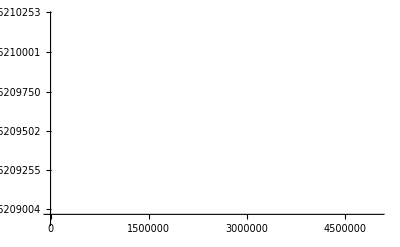

Limit of daACE(t) = {0.00207704}

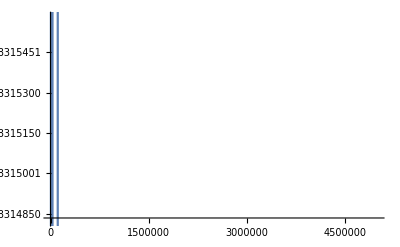

Limit of daCUP(t) = {0.0000688661}

-Graphics-

Limit of dCTR(t) = {0.00347423}

-Graphics-

Limit of dCU(t) = {2.15524}

-Graphics-

Limit of dMAC(t) = {0.38109}

-Graphics-

Limit of dACE(t) = {0.462923}

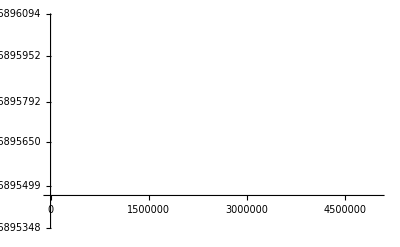

Limit of dCUP(t) = {4.18502}

-Graphics-

Limit of daCOX(t) = {2.46304}

-Graphics-

Limit of dCOX(t) = {1.48926}

```mathematica
COPPER = 250;
SYSTEM = COPPER - 13;

(*CUINC = (kINL [[SYSTEM]]* dCTR[t] * COPPER / (KMIN +COPPER)) + KNEW*COPPER;*)
CUINC = (kINL [[SYSTEM]]* dCTR[t] * COPPER / (KMIN +COPPER));
BMACC = kAMACL[[SYSTEM]];
BACEC = kAACEL[[SYSTEM]];
BCOXC = kACOXL[[SYSTEM]];
BCUPC = kACUPL[[SYSTEM]] * dACE[t];
BCTRC = kCTRL[[SYSTEM]] * daMAC[t];
MMACFC = kMACFL[[SYSTEM]] * daMAC[t] * dCU[t]^4;
MMACRC = kMACRL[[SYSTEM]] * dMAC[t];
MACEFC = kACEFL[[SYSTEM]] * daACE[t] * dCU[t]^4;
MACERC = kACERL[[SYSTEM]] * dACE[t];
MCUPFC = kCUPFL[[SYSTEM]] * daCUP[t] * dCU[t]^8;
MCUPRC = kCUPRL[[SYSTEM]] * dCUP[t];
MCOXFC = kCOXFL[[SYSTEM]] * daCOX[t] * dCU[t];
MCOXRC = kCOXRL[[SYSTEM]] * dCOX[t];

DAACEC = ALPHA * daACE[t];
DACEC = ALPHA * dACE[t];
DACOXC = ALPHA * daCOX[t];
DCOXC = ALPHA * dCOX[t];
DCTRC = ALPHA * dCTR[t];
DACUPC = ALPHA * daCUP[t];
DCUPC = ALPHA * dCUP[t];
DAMACC = ALPHA * daMAC[t];
DMACC = ALPHA * dMAC[t];
DCUC = ALPHA * dCU[t];

(*aMAC'*) diffeq1 = daMAC'[t] == BMACC - MMACFC + MMACRC - DAMACC;
(*aACE'*)diffeq2 = daACE'[t] == BACEC - MACEFC + MACERC - DAACEC;
(*aCUP'*)diffeq3 = daCUP'[t] ==BCUPC - MCUPFC + MCUPRC - DACUPC;
(*CTR'*)diffeq4 = dCTR'[t] == BCTRC - DCTRC;
(*CU'*)diffeq5 = dCU'[t] == CUINC - 4*MMACFC + 4*MMACRC - 4*MACEFC + 4*MACERC - 8*MCUPFC + 8*MCUPRC - MCOXFC + MCOXRC - DCUC;
(*MAC'*)diffeq6 = dMAC'[t] == MMACFC - MMACRC - DMACC;
(*ACE'*)diffeq7 = dACE'[t] == MACEFC - MACERC - DACEC;
(*CUP'*)diffeq8 = dCUP'[t] == MCUPFC - MCUPRC - DCUPC;
(*aCOX'*)diffeq9 = daCOX'[t] == BCOXC - MCOXFC + MCOXRC - DACOXC;
(*COX'*)diffeq10 = dCOX'[t] == MCOXFC - MCOXRC - DCOXC;

eqns={diffeq1,diffeq2,diffeq3,diffeq4,diffeq5,diffeq6,diffeq7,diffeq8, diffeq9, diffeq10, daMAC[0] == AMAC[[SYSTEM]], daACE[0] == ACE[[SYSTEM]], daCUP[0] == ACUP[[SYSTEM]], dCTR[0] == CTR[[SYSTEM]], dCU[0] == CU[[SYSTEM]], dMAC[0] == MAC[[SYSTEM]], dACE[0] == ACE[[SYSTEM]], dCUP[0] == CUP[[SYSTEM]], daCOX[0] == ACOX[[SYSTEM]], dCOX[0] == COX[[SYSTEM]]};
s=NDSolve[eqns,{daMAC, daACE, daCUP, dCTR, dCU, dMAC, dACE, dCUP, daCOX, dCOX},{t,0,5000000}];
<<NumericalCalculus`;

(*1*)
Plot[Evaluate[daMAC[t]/. s],{t,0,500000}]
Print["Limit of daMAC(t) = ",daMAC[5000000]/. s]
(*2*)
Plot[Evaluate[daACE[t]/. s],{t,0,5000000}]
Print["Limit of daACE(t) = ",daACE[5000000]/. s]
(*3*)
Plot[Evaluate[daCUP[t]/. s],{t,0,5000000}]
Print["Limit of daCUP(t) = ",daCUP[5000000]/. s]
(*4*)
Plot[Evaluate[dCTR[t]/. s],{t,0,5000000}]
Print["Limit of dCTR(t) = ",dCTR[5000000]/. s]
(*5*)
Plot[Evaluate[dCU[t]/. s],{t,0,5000000}]
Print["Limit of dCU(t) = ",dCU[5000000]/. s]
(*6*)
Plot[Evaluate[dMAC[t]/. s],{t,0,5000000}]
Print["Limit of dMAC(t) = ",dMAC[5000000]/. s]
(*7*)
Plot[Evaluate[dACE[t]/. s],{t,0,5000000}]
Print["Limit of dACE(t) = ",dACE[5000000]/. s]
(*8*)
Plot[Evaluate[dCUP[t]/. s],{t,0,5000000}]
Print["Limit of dCUP(t) = ",dCUP[5000000]/. s]
(*9*)
Plot[Evaluate[daCOX[t]/. s],{t,0,5000000}]
Print["Limit of daCOX(t) = ",daCOX[5000000]/. s]
(*10*)
Plot[Evaluate[dCOX[t]/. s],{t,0,5000000}]
Print["Limit of dCOX(t) = ",dCOX[5000000]/. s]
```

```mathematica
7
```